```mathematica
optsLabel1=Sequence[FontFamily->"Helvetica",FontSize->22];
optsLabel2=Sequence[FontFamily->"Helvetica",FontSize->22,Transparent];
optsCentrality=Sequence[FontFamily->"Helvetica",FontSize->18];
optsCentrality2=Sequence[FontFamily->"Helvetica",FontSize->18,Transparent];
optsScale1=Sequence[FontFamily->"Helvetica",FontSize->16];
optsScale2=Sequence[FontFamily->"Helvetica",FontSize->16,Transparent];
```

```mathematica
r=(√(1+(8 ct)/α) (1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4)^2)/(α/2(√(1+(8 ct)/α)-1) (1-ω/p(α/4(√(1+(8 ct)/α)-1))^4));
```

```mathematica
s=(α/2(√(1+(8 ct)/α)-1) (1-ω/p(α/4(√(1+(8 ct)/α)-1))^4)ct)/(√(1+(8 ct)/α) (1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4)^2)-(α/4(√(1+(8 ct)/α)-1))^2/(1+(1+1/p)(α/4(√(1+(8 ct)/α)-1))^2 +ω/p(α/4(√(1+(8 ct)/α)-1))^4);
```

```mathematica
α=√(1600/5.6)
p=25.
```

16.9031

25.

We first change ω, with p=25.

```mathematica
ω=5.
```

5.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.852,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.517,0.000035894,0.006},{62.6858,0.0000637458,0.008},{50.1878,0.0000994978,0.01},{41.8566,0.000143122,0.012},{35.9063,0.000194591,0.014},{31.444,0.000253873,0.016},{27.9739,0.000320938,0.018},{25.1982,0.000395754,0.02},{22.9276,0.000478289,0.022},{21.0357,0.000568507,0.024},{19.4352,0.000666375,0.026},{18.0637,0.000771856,0.028},{16.8753,0.000884912,0.03},{15.8357,0.00100551,0.032},{14.9187,0.0011336,0.034},{14.1038,0.00126915,0.036},{13.3749,0.00141212,0.038},{12.7191,0.00156247,0.04},{12.1259,0.00172014,0.042},{11.5869,0.00188511,0.044},{11.0949,0.00205732,0.046},{10.6441,0.00223673,0.048},{10.2295,0.00242329,0.05},{9.84703,0.00261695,0.052},{9.49301,0.00281767,0.054},{9.16443,0.0030254,0.056},{8.85866,0.00324008,0.058},{8.57342,0.00346167,0.06},{8.30672,0.0036901,0.062},{8.05682,0.00392534,0.064},{7.82219,0.00416733,0.066},{7.6015,0.00441601,0.068},{7.39354,0.00467132,0.07},{7.19725,0.00493322,0.072},{7.01169,0.00520164,0.074},{6.83601,0.00547652,0.076},{6.66945,0.00575782,0.078},{6.51133,0.00604546,0.08},{6.36103,0.00633939,0.082},{6.21799,0.00663955,0.084},{6.08171,0.00694588,0.086},{5.95172,0.00725831,0.088},{5.82761,0.00757678,0.09},{5.70898,0.00790124,0.092},{5.5955,0.00823161,0.094},{5.48685,0.00856782,0.096},{5.38271,0.00890983,0.098},{5.28284,0.00925755,0.1},{5.18696,0.00961093,0.102},{5.09486,0.00996989,0.104},{5.00632,0.0103344,0.106},{4.92115,0.0107043,0.108},{4.83915,0.0110796,0.11},{4.76016,0.0114602,0.112},{4.68402,0.0118461,0.114},{4.61059,0.0122371,0.116},{4.53973,0.0126332,0.118},{4.4713,0.0130344,0.12},{4.40519,0.0134405,0.122},{4.34129,0.0138515,0.124},{4.27949,0.0142673,0.126},{4.21969,0.0146878,0.128},{4.16181,0.015113,0.13},{4.10574,0.0155428,0.132},{4.05143,0.0159771,0.134},{3.99878,0.0164159,0.136},{3.94772,0.016859,0.138},{3.89819,0.0173063,0.14},{3.85012,0.0177579,0.142},{3.80345,0.0182137,0.144},{3.75813,0.0186734,0.146},{3.71409,0.0191372,0.148},{3.67129,0.0196048,0.15},{3.62969,0.0200763,0.152},{3.58922,0.0205515,0.154},{3.54986,0.0210304,0.156},{3.51155,0.0215129,0.158},{3.47426,0.0219989,0.16},{3.43795,0.0224883,0.162},{3.40259,0.022981,0.164},{3.36814,0.023477,0.166},{3.33457,0.0239762,0.168},{3.30184,0.0244785,0.17},{3.26993,0.0249839,0.172},{3.23882,0.0254921,0.174},{3.20847,0.0260033,0.176},{3.17885,0.0265172,0.178},{3.14995,0.0270338,0.18},{3.12174,0.027553,0.182},{3.0942,0.0280748,0.184},{3.06731,0.0285991,0.186},{3.04104,0.0291257,0.188},{3.01538,0.0296546,0.19},{2.99031,0.0301857,0.192},{2.9658,0.0307189,0.194},{2.94185,0.0312542,0.196},{2.91844,0.0317914,0.198},{2.89554,0.0323305,0.2},{2.87316,0.0328715,0.202},{2.85126,0.0334141,0.204},{2.82983,0.0339584,0.206},{2.80888,0.0345042,0.208},{2.78837,0.0350515,0.21},{2.76829,0.0356002,0.212},{2.74864,0.0361502,0.214},{2.72941,0.0367014,0.216},{2.71058,0.0372538,0.218},{2.69214,0.0378072,0.22},{2.67408,0.0383616,0.222},{2.65639,0.0389169,0.224},{2.63906,0.039473,0.226},{2.62209,0.0400298,0.228},{2.60546,0.0405873,0.23},{2.58916,0.0411454,0.232},{2.57319,0.0417039,0.234},{2.55754,0.0422629,0.236},{2.54219,0.0428222,0.238},{2.52715,0.0433817,0.24},{2.51241,0.0439414,0.242},{2.49795,0.0445012,0.244},{2.48377,0.0450609,0.246},{2.46987,0.0456207,0.248},{2.45624,0.0461802,0.25},{2.44287,0.0467395,0.252},{2.42975,0.0472985,0.254},{2.41689,0.0478571,0.256},{2.40427,0.0484153,0.258},{2.39189,0.0489729,0.26},{2.37974,0.0495298,0.262},{2.36782,0.0500861,0.264},{2.35613,0.0506415,0.266},{2.34466,0.0511961,0.268},{2.33339,0.0517498,0.27},{2.32234,0.0523025,0.272},{2.3115,0.052854,0.274},{2.30085,0.0534044,0.276},{2.29041,0.0539535,0.278},{2.28015,0.0545014,0.28},{2.27009,0.0550478,0.282},{2.26021,0.0555927,0.284},{2.25051,0.0561361,0.286},{2.24099,0.0566779,0.288},{2.23164,0.057218,0.29},{2.22247,0.0577564,0.292},{2.21346,0.0582928,0.294},{2.20462,0.0588274,0.296},{2.19593,0.05936,0.298},{2.18741,0.0598905,0.3},{2.17904,0.0604189,0.302},{2.17083,0.0609451,0.304},{2.16276,0.0614691,0.306},{2.15485,0.0619907,0.308},{2.14707,0.0625099,0.31},{2.13944,0.0630266,0.312},{2.13195,0.0635407,0.314},{2.12459,0.0640522,0.316},{2.11737,0.0645611,0.318},{2.11028,0.0650672,0.32},{2.10332,0.0655705,0.322},{2.09649,0.0660709,0.324},{2.08978,0.0665683,0.326},{2.0832,0.0670627,0.328},{2.07674,0.0675541,0.33},{2.0704,0.0680423,0.332},{2.06418,0.0685272,0.334},{2.05807,0.069009,0.336},{2.05207,0.0694873,0.338},{2.04619,0.0699623,0.34},{2.04042,0.0704338,0.342},{2.03475,0.0709017,0.344},{2.02919,0.0713661,0.346},{2.02374,0.0718269,0.348},{2.01839,0.0722839,0.35},{2.01315,0.0727372,0.352},{2.008,0.0731866,0.354},{2.00295,0.0736321,0.356},{1.998,0.0740737,0.358},{1.99315,0.0745113,0.36},{1.98839,0.0749449,0.362},{1.98372,0.0753743,0.364},{1.97915,0.0757996,0.366},{1.97466,0.0762206,0.368},{1.97027,0.0766374,0.37},{1.96596,0.0770498,0.372},{1.96174,0.0774578,0.374},{1.95761,0.0778614,0.376},{1.95356,0.0782605,0.378},{1.9496,0.0786551,0.38},{1.94571,0.079045,0.382},{1.94191,0.0794303,0.384},{1.93819,0.0798109,0.386},{1.93455,0.0801868,0.388},{1.93099,0.0805579,0.39},{1.9275,0.0809241,0.392},{1.92409,0.0812854,0.394},{1.92076,0.0816418,0.396},{1.9175,0.0819932,0.398},{1.91431,0.0823396,0.4},{1.9112,0.0826809,0.402},{1.90815,0.083017,0.404},{1.90518,0.083348,0.406},{1.90228,0.0836738,0.408},{1.89945,0.0839943,0.41},{1.89669,0.0843095,0.412},{1.89399,0.0846194,0.414},{1.89136,0.0849239,0.416},{1.8888,0.085223,0.418},{1.8863,0.0855166,0.42},{1.88387,0.0858047,0.422},{1.8815,0.0860873,0.424},{1.8792,0.0863643,0.426},{1.87696,0.0866357,0.428},{1.87478,0.0869014,0.43},{1.87266,0.0871614,0.432},{1.8706,0.0874157,0.434},{1.86861,0.0876642,0.436},{1.86667,0.0879069,0.438},{1.86479,0.0881438,0.44},{1.86297,0.0883748,0.442},{1.86121,0.0886,0.444},{1.8595,0.0888191,0.446},{1.85786,0.0890324,0.448},{1.85626,0.0892396,0.45},{1.85473,0.0894408,0.452},{1.85325,0.0896359,0.454},{1.85182,0.0898249,0.456},{1.85045,0.0900078,0.458},{1.84913,0.0901846,0.46},{1.84787,0.0903552,0.462},{1.84666,0.0905196,0.464},{1.8455,0.0906778,0.466},{1.84439,0.0908297,0.468},{1.84333,0.0909753,0.47},{1.84233,0.0911146,0.472},{1.84138,0.0912476,0.474},{1.84047,0.0913742,0.476},{1.83962,0.0914945,0.478},{1.83882,0.0916083,0.48},{1.83806,0.0917157,0.482},{1.83735,0.0918167,0.484},{1.8367,0.0919112,0.486},{1.83609,0.0919992,0.488},{1.83553,0.0920807,0.49},{1.83501,0.0921557,0.492},{1.83454,0.0922242,0.494},{1.83412,0.092286,0.496},{1.83375,0.0923413,0.498},{1.83342,0.09239,0.5},{1.83314,0.0924321,0.502},{1.8329,0.0924675,0.504},{1.83271,0.0924963,0.506},{1.83256,0.0925184,0.508},{1.83246,0.0925338,0.51},{1.83241,0.0925426,0.512},{1.83239,0.0925446,0.514},{1.83242,0.0925399,0.516},{1.8325,0.0925285,0.518},{1.83261,0.0925103,0.52},{1.83277,0.0924854,0.522},{1.83298,0.0924537,0.524},{1.83322,0.0924152,0.526},{1.83351,0.09237,0.528},{1.83384,0.0923179,0.53},{1.83422,0.092259,0.532},{1.83463,0.0921933,0.534},{1.83509,0.0921208,0.536},{1.83559,0.0920415,0.538},{1.83612,0.0919553,0.54},{1.8367,0.0918623,0.542},{1.83733,0.0917624,0.544},{1.83799,0.0916557,0.546},{1.83869,0.0915421,0.548},{1.83943,0.0914217,0.55},{1.84021,0.0912943,0.552},{1.84103,0.0911601,0.554},{1.8419,0.0910191,0.556},{1.8428,0.0908711,0.558},{1.84374,0.0907163,0.56},{1.84472,0.0905545,0.562},{1.84574,0.0903859,0.564},{1.8468,0.0902104,0.566},{1.8479,0.0900281,0.568},{1.84903,0.0898388,0.57},{1.85021,0.0896427,0.572},{1.85142,0.0894396,0.574},{1.85267,0.0892297,0.576},{1.85396,0.0890129,0.578},{1.85529,0.0887892,0.58},{1.85666,0.0885587,0.582},{1.85806,0.0883212,0.584},{1.85951,0.0880769,0.586},{1.86099,0.0878258,0.588},{1.86251,0.0875677,0.59},{1.86406,0.0873028,0.592},{1.86566,0.0870311,0.594},{1.86729,0.0867525,0.596},{1.86896,0.0864671,0.598},{1.87066,0.0861748,0.6},{1.87241,0.0858757,0.602},{1.87419,0.0855698,0.604},{1.876,0.0852571,0.606},{1.87786,0.0849376,0.608},{1.87975,0.0846112,0.61},{1.88168,0.0842781,0.612},{1.88364,0.0839382,0.614},{1.88564,0.0835915,0.616},{1.88768,0.0832381,0.618},{1.88976,0.0828779,0.62},{1.89187,0.082511,0.622},{1.89402,0.0821374,0.624},{1.89621,0.081757,0.626},{1.89843,0.0813699,0.628},{1.90069,0.0809762,0.63},{1.90298,0.0805757,0.632},{1.90531,0.0801686,0.634},{1.90768,0.0797548,0.636},{1.91009,0.0793344,0.638},{1.91253,0.0789073,0.64},{1.91501,0.0784737,0.642},{1.91752,0.0780334,0.644},{1.92007,0.0775865,0.646},{1.92266,0.0771331,0.648},{1.92528,0.0766731,0.65},{1.92794,0.0762066,0.652},{1.93064,0.0757335,0.654},{1.93337,0.0752539,0.656},{1.93614,0.0747678,0.658},{1.93895,0.0742753,0.66},{1.94179,0.0737763,0.662},{1.94467,0.0732708,0.664},{1.94758,0.0727589,0.666},{1.95054,0.0722406,0.668},{1.95353,0.071716,0.67},{1.95655,0.0711849,0.672},{1.95961,0.0706475,0.674},{1.96271,0.0701037,0.676},{1.96585,0.0695536,0.678},{1.96902,0.0689973,0.68},{1.97223,0.0684346,0.682},{1.97547,0.0678657,0.684},{1.97875,0.0672906,0.686},{1.98207,0.0667092,0.688},{1.98543,0.0661216,0.69},{1.98882,0.0655279,0.692},{1.99225,0.064928,0.694},{1.99572,0.064322,0.696},{1.99922,0.0637098,0.698},{2.00276,0.0630916,0.7},{2.00634,0.0624672,0.702},{2.00996,0.0618369,0.704},{2.01361,0.0612005,0.706},{2.0173,0.0605581,0.708},{2.02103,0.0599097,0.71},{2.0248,0.0592554,0.712},{2.0286,0.0585951,0.714},{2.03244,0.0579289,0.716},{2.03632,0.0572569,0.718},{2.04024,0.0565789,0.72},{2.04419,0.0558952,0.722},{2.04819,0.0552056,0.724},{2.05222,0.0545102,0.726},{2.05629,0.053809,0.728},{2.0604,0.0531021,0.73},{2.06454,0.0523895,0.732},{2.06873,0.0516712,0.734},{2.07295,0.0509472,0.736},{2.07722,0.0502176,0.738},{2.08152,0.0494823,0.74},{2.08586,0.0487415,0.742},{2.09024,0.0479951,0.744},{2.09466,0.0472431,0.746},{2.09912,0.0464856,0.748},{2.10361,0.0457227,0.75},{2.10815,0.0449543,0.752},{2.11273,0.0441804,0.754},{2.11735,0.0434011,0.756},{2.122,0.0426165,0.758},{2.1267,0.0418265,0.76},{2.13144,0.0410311,0.762},{2.13622,0.0402305,0.764},{2.14103,0.0394245,0.766},{2.14589,0.0386134,0.768},{2.15079,0.037797,0.77},{2.15573,0.0369754,0.772},{2.16072,0.0361486,0.774},{2.16574,0.0353167,0.776},{2.1708,0.0344797,0.778},{2.17591,0.0336376,0.78},{2.18106,0.0327905,0.782},{2.18625,0.0319383,0.784},{2.19148,0.0310811,0.786},{2.19675,0.030219,0.788},{2.20207,0.0293519,0.79},{2.20743,0.0284799,0.792},{2.21283,0.027603,0.794},{2.21827,0.0267213,0.796},{2.22376,0.0258347,0.798},{2.22929,0.0249434,0.8},{2.23486,0.0240472,0.802},{2.24048,0.0231463,0.804},{2.24614,0.0222408,0.806},{2.25185,0.0213305,0.808},{2.2576,0.0204155,0.81},{2.26339,0.019496,0.812},{2.26923,0.0185718,0.814},{2.27511,0.0176431,0.816},{2.28104,0.0167099,0.818},{2.28701,0.0157721,0.82},{2.29303,0.0148299,0.822},{2.2991,0.0138832,0.824},{2.30521,0.0129321,0.826},{2.31136,0.0119766,0.828},{2.31757,0.0110167,0.83},{2.32381,0.0100525,0.832},{2.33011,0.00908404,0.834},{2.33645,0.00811128,0.836},{2.34284,0.00713428,0.838},{2.34928,0.00615307,0.84},{2.35576,0.00516767,0.842},{2.3623,0.00417813,0.844},{2.36888,0.00318446,0.846},{2.37551,0.0021867,0.848},{2.38218,0.00118488,0.85},{2.38891,0.000179028,0.852}}

```mathematica
ddEsp5=Table[{cc[[i,1]],cc[[i,2]]},{i,1,426,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.517,0.000035894},{62.6858,0.0000637458},{50.1878,0.0000994978},{41.8566,0.000143122},{35.9063,0.000194591},{31.444,0.000253873},{27.9739,0.000320938},{25.1982,0.000395754},{22.9276,0.000478289},{21.0357,0.000568507},{19.4352,0.000666375},{18.0637,0.000771856},{16.8753,0.000884912},{15.8357,0.00100551},{14.9187,0.0011336},{14.1038,0.00126915},{13.3749,0.00141212},{12.7191,0.00156247},{12.1259,0.00172014},{11.5869,0.00188511},{11.0949,0.00205732},{10.6441,0.00223673},{10.2295,0.00242329},{9.84703,0.00261695},{9.49301,0.00281767},{9.16443,0.0030254},{8.85866,0.00324008},{8.57342,0.00346167},{8.30672,0.0036901},{8.05682,0.00392534},{7.82219,0.00416733},{7.6015,0.00441601},{7.39354,0.00467132},{7.19725,0.00493322},{7.01169,0.00520164},{6.83601,0.00547652},{6.66945,0.00575782},{6.51133,0.00604546},{6.36103,0.00633939},{6.21799,0.00663955},{6.08171,0.00694588},{5.95172,0.00725831},{5.82761,0.00757678},{5.70898,0.00790124},{5.5955,0.00823161},{5.48685,0.00856782},{5.38271,0.00890983},{5.28284,0.00925755},{5.18696,0.00961093},{5.09486,0.00996989},{5.00632,0.0103344},{4.92115,0.0107043},{4.83915,0.0110796},{4.76016,0.0114602},{4.68402,0.0118461},{4.61059,0.0122371},{4.53973,0.0126332},{4.4713,0.0130344},{4.40519,0.0134405},{4.34129,0.0138515},{4.27949,0.0142673},{4.21969,0.0146878},{4.16181,0.015113},{4.10574,0.0155428},{4.05143,0.0159771},{3.99878,0.0164159},{3.94772,0.016859},{3.89819,0.0173063},{3.85012,0.0177579},{3.80345,0.0182137},{3.75813,0.0186734},{3.71409,0.0191372},{3.67129,0.0196048},{3.62969,0.0200763},{3.58922,0.0205515},{3.54986,0.0210304},{3.51155,0.0215129},{3.47426,0.0219989},{3.43795,0.0224883},{3.40259,0.022981},{3.36814,0.023477},{3.33457,0.0239762},{3.30184,0.0244785},{3.26993,0.0249839},{3.23882,0.0254921},{3.20847,0.0260033},{3.17885,0.0265172},{3.14995,0.0270338},{3.12174,0.027553},{3.0942,0.0280748},{3.06731,0.0285991},{3.04104,0.0291257},{3.01538,0.0296546},{2.99031,0.0301857},{2.9658,0.0307189},{2.94185,0.0312542},{2.91844,0.0317914},{2.89554,0.0323305},{2.87316,0.0328715},{2.85126,0.0334141},{2.82983,0.0339584},{2.80888,0.0345042},{2.78837,0.0350515},{2.76829,0.0356002},{2.74864,0.0361502},{2.72941,0.0367014},{2.71058,0.0372538},{2.69214,0.0378072},{2.67408,0.0383616},{2.65639,0.0389169},{2.63906,0.039473},{2.62209,0.0400298},{2.60546,0.0405873},{2.58916,0.0411454},{2.57319,0.0417039},{2.55754,0.0422629},{2.54219,0.0428222},{2.52715,0.0433817},{2.51241,0.0439414},{2.49795,0.0445012},{2.48377,0.0450609},{2.46987,0.0456207},{2.45624,0.0461802},{2.44287,0.0467395},{2.42975,0.0472985},{2.41689,0.0478571},{2.40427,0.0484153},{2.39189,0.0489729},{2.37974,0.0495298},{2.36782,0.0500861},{2.35613,0.0506415},{2.34466,0.0511961},{2.33339,0.0517498},{2.32234,0.0523025},{2.3115,0.052854},{2.30085,0.0534044},{2.29041,0.0539535},{2.28015,0.0545014},{2.27009,0.0550478},{2.26021,0.0555927},{2.25051,0.0561361},{2.24099,0.0566779},{2.23164,0.057218},{2.22247,0.0577564},{2.21346,0.0582928},{2.20462,0.0588274},{2.19593,0.05936},{2.18741,0.0598905},{2.17904,0.0604189},{2.17083,0.0609451},{2.16276,0.0614691},{2.15485,0.0619907},{2.14707,0.0625099},{2.13944,0.0630266},{2.13195,0.0635407},{2.12459,0.0640522},{2.11737,0.0645611},{2.11028,0.0650672},{2.10332,0.0655705},{2.09649,0.0660709},{2.08978,0.0665683},{2.0832,0.0670627},{2.07674,0.0675541},{2.0704,0.0680423},{2.06418,0.0685272},{2.05807,0.069009},{2.05207,0.0694873},{2.04619,0.0699623},{2.04042,0.0704338},{2.03475,0.0709017},{2.02919,0.0713661},{2.02374,0.0718269},{2.01839,0.0722839},{2.01315,0.0727372},{2.008,0.0731866},{2.00295,0.0736321},{1.998,0.0740737},{1.99315,0.0745113},{1.98839,0.0749449},{1.98372,0.0753743},{1.97915,0.0757996},{1.97466,0.0762206},{1.97027,0.0766374},{1.96596,0.0770498},{1.96174,0.0774578},{1.95761,0.0778614},{1.95356,0.0782605},{1.9496,0.0786551},{1.94571,0.079045},{1.94191,0.0794303},{1.93819,0.0798109},{1.93455,0.0801868},{1.93099,0.0805579},{1.9275,0.0809241},{1.92409,0.0812854},{1.92076,0.0816418},{1.9175,0.0819932},{1.91431,0.0823396},{1.9112,0.0826809},{1.90815,0.083017},{1.90518,0.083348},{1.90228,0.0836738},{1.89945,0.0839943},{1.89669,0.0843095},{1.89399,0.0846194},{1.89136,0.0849239},{1.8888,0.085223},{1.8863,0.0855166},{1.88387,0.0858047},{1.8815,0.0860873},{1.8792,0.0863643},{1.87696,0.0866357},{1.87478,0.0869014},{1.87266,0.0871614},{1.8706,0.0874157},{1.86861,0.0876642},{1.86667,0.0879069},{1.86479,0.0881438},{1.86297,0.0883748},{1.86121,0.0886},{1.8595,0.0888191},{1.85786,0.0890324},{1.85626,0.0892396},{1.85473,0.0894408},{1.85325,0.0896359},{1.85182,0.0898249},{1.85045,0.0900078},{1.84913,0.0901846},{1.84787,0.0903552},{1.84666,0.0905196},{1.8455,0.0906778},{1.84439,0.0908297},{1.84333,0.0909753},{1.84233,0.0911146},{1.84138,0.0912476},{1.84047,0.0913742},{1.83962,0.0914945},{1.83882,0.0916083},{1.83806,0.0917157},{1.83735,0.0918167},{1.8367,0.0919112},{1.83609,0.0919992},{1.83553,0.0920807},{1.83501,0.0921557},{1.83454,0.0922242},{1.83412,0.092286},{1.83375,0.0923413},{1.83342,0.09239},{1.83314,0.0924321},{1.8329,0.0924675},{1.83271,0.0924963},{1.83256,0.0925184},{1.83246,0.0925338},{1.83241,0.0925426},{1.83239,0.0925446},{1.83242,0.0925399},{1.8325,0.0925285},{1.83261,0.0925103},{1.83277,0.0924854},{1.83298,0.0924537},{1.83322,0.0924152},{1.83351,0.09237},{1.83384,0.0923179},{1.83422,0.092259},{1.83463,0.0921933},{1.83509,0.0921208},{1.83559,0.0920415},{1.83612,0.0919553},{1.8367,0.0918623},{1.83733,0.0917624},{1.83799,0.0916557},{1.83869,0.0915421},{1.83943,0.0914217},{1.84021,0.0912943},{1.84103,0.0911601},{1.8419,0.0910191},{1.8428,0.0908711},{1.84374,0.0907163},{1.84472,0.0905545},{1.84574,0.0903859},{1.8468,0.0902104},{1.8479,0.0900281},{1.84903,0.0898388},{1.85021,0.0896427},{1.85142,0.0894396},{1.85267,0.0892297},{1.85396,0.0890129},{1.85529,0.0887892},{1.85666,0.0885587},{1.85806,0.0883212},{1.85951,0.0880769},{1.86099,0.0878258},{1.86251,0.0875677},{1.86406,0.0873028},{1.86566,0.0870311},{1.86729,0.0867525},{1.86896,0.0864671},{1.87066,0.0861748},{1.87241,0.0858757},{1.87419,0.0855698},{1.876,0.0852571},{1.87786,0.0849376},{1.87975,0.0846112},{1.88168,0.0842781},{1.88364,0.0839382},{1.88564,0.0835915},{1.88768,0.0832381},{1.88976,0.0828779},{1.89187,0.082511},{1.89402,0.0821374},{1.89621,0.081757},{1.89843,0.0813699},{1.90069,0.0809762},{1.90298,0.0805757},{1.90531,0.0801686},{1.90768,0.0797548},{1.91009,0.0793344},{1.91253,0.0789073},{1.91501,0.0784737},{1.91752,0.0780334},{1.92007,0.0775865},{1.92266,0.0771331},{1.92528,0.0766731},{1.92794,0.0762066},{1.93064,0.0757335},{1.93337,0.0752539},{1.93614,0.0747678},{1.93895,0.0742753},{1.94179,0.0737763},{1.94467,0.0732708},{1.94758,0.0727589},{1.95054,0.0722406},{1.95353,0.071716},{1.95655,0.0711849},{1.95961,0.0706475},{1.96271,0.0701037},{1.96585,0.0695536},{1.96902,0.0689973},{1.97223,0.0684346},{1.97547,0.0678657},{1.97875,0.0672906},{1.98207,0.0667092},{1.98543,0.0661216},{1.98882,0.0655279},{1.99225,0.064928},{1.99572,0.064322},{1.99922,0.0637098},{2.00276,0.0630916},{2.00634,0.0624672},{2.00996,0.0618369},{2.01361,0.0612005},{2.0173,0.0605581},{2.02103,0.0599097},{2.0248,0.0592554},{2.0286,0.0585951},{2.03244,0.0579289},{2.03632,0.0572569},{2.04024,0.0565789},{2.04419,0.0558952},{2.04819,0.0552056},{2.05222,0.0545102},{2.05629,0.053809},{2.0604,0.0531021},{2.06454,0.0523895},{2.06873,0.0516712},{2.07295,0.0509472},{2.07722,0.0502176},{2.08152,0.0494823},{2.08586,0.0487415},{2.09024,0.0479951},{2.09466,0.0472431},{2.09912,0.0464856},{2.10361,0.0457227},{2.10815,0.0449543},{2.11273,0.0441804},{2.11735,0.0434011},{2.122,0.0426165},{2.1267,0.0418265},{2.13144,0.0410311},{2.13622,0.0402305},{2.14103,0.0394245},{2.14589,0.0386134},{2.15079,0.037797},{2.15573,0.0369754},{2.16072,0.0361486},{2.16574,0.0353167},{2.1708,0.0344797},{2.17591,0.0336376},{2.18106,0.0327905},{2.18625,0.0319383},{2.19148,0.0310811},{2.19675,0.030219},{2.20207,0.0293519},{2.20743,0.0284799},{2.21283,0.027603},{2.21827,0.0267213},{2.22376,0.0258347},{2.22929,0.0249434},{2.23486,0.0240472},{2.24048,0.0231463},{2.24614,0.0222408},{2.25185,0.0213305},{2.2576,0.0204155},{2.26339,0.019496},{2.26923,0.0185718},{2.27511,0.0176431},{2.28104,0.0167099},{2.28701,0.0157721},{2.29303,0.0148299},{2.2991,0.0138832},{2.30521,0.0129321},{2.31136,0.0119766},{2.31757,0.0110167},{2.32381,0.0100525},{2.33011,0.00908404},{2.33645,0.00811128},{2.34284,0.00713428},{2.34928,0.00615307},{2.35576,0.00516767},{2.3623,0.00417813},{2.36888,0.00318446},{2.37551,0.0021867},{2.38218,0.00118488},{2.38891,0.000179028}}

```mathematica
ω=50.
```

50.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.594,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.517,0.000035894,0.006},{62.6858,0.0000637458,0.008},{50.1878,0.0000994978,0.01},{41.8566,0.000143122,0.012},{35.9063,0.00019459,0.014},{31.4441,0.000253873,0.016},{27.9739,0.000320938,0.018},{25.1982,0.000395754,0.02},{22.9276,0.000478288,0.022},{21.0357,0.000568506,0.024},{19.4353,0.000666372,0.026},{18.0637,0.000771851,0.028},{16.8753,0.000884906,0.03},{15.8358,0.0010055,0.032},{14.9188,0.00113359,0.034},{14.1039,0.00126913,0.036},{13.375,0.00141209,0.038},{12.7192,0.00156243,0.04},{12.1261,0.0017201,0.042},{11.5871,0.00188505,0.044},{11.0952,0.00205724,0.046},{10.6444,0.00223662,0.048},{10.2299,0.00242316,0.05},{9.84741,0.00261678,0.052},{9.49344,0.00281746,0.054},{9.16491,0.00302514,0.056},{8.85919,0.00323976,0.058},{8.574,0.00346127,0.06},{8.30736,0.00368963,0.062},{8.05752,0.00392476,0.064},{7.82297,0.00416663,0.066},{7.60235,0.00441518,0.068},{7.39446,0.00467034,0.07},{7.19826,0.00493205,0.072},{7.01278,0.00520027,0.074},{6.8372,0.00547492,0.076},{6.67073,0.00575595,0.078},{6.51272,0.00604329,0.08},{6.36252,0.00633688,0.082},{6.21959,0.00663666,0.084},{6.08343,0.00694256,0.086},{5.95356,0.00725451,0.088},{5.82958,0.00757245,0.09},{5.71109,0.00789631,0.092},{5.59775,0.00822601,0.094},{5.48924,0.00856149,0.096},{5.38526,0.00890268,0.098},{5.28554,0.00924951,0.1},{5.18983,0.00960189,0.102},{5.09791,0.00995977,0.104},{5.00955,0.0103231,0.106},{4.92456,0.0106917,0.108},{4.84276,0.0110656,0.11},{4.76397,0.0114446,0.112},{4.68804,0.0118288,0.114},{4.61483,0.012218,0.116},{4.54419,0.0126121,0.118},{4.47599,0.0130111,0.12},{4.41012,0.0134148,0.122},{4.34647,0.0138233,0.124},{4.28493,0.0142363,0.126},{4.2254,0.0146539,0.128},{4.16779,0.0150759,0.13},{4.11201,0.0155022,0.132},{4.05798,0.0159328,0.134},{4.00563,0.0163676,0.136},{3.95489,0.0168065,0.138},{3.90568,0.0172493,0.14},{3.85794,0.017696,0.142},{3.81161,0.0181465,0.144},{3.76663,0.0186008,0.146},{3.72296,0.0190586,0.148},{3.68053,0.01952,0.15},{3.6393,0.0199847,0.152},{3.59923,0.0204528,0.154},{3.56027,0.0209241,0.156},{3.52237,0.0213985,0.158},{3.48551,0.0218759,0.16},{3.44964,0.0223563,0.162},{3.41472,0.0228394,0.164},{3.38073,0.0233253,0.166},{3.34762,0.0238138,0.168},{3.31538,0.0243047,0.17},{3.28397,0.0247981,0.172},{3.25336,0.0252937,0.174},{3.22352,0.0257915,0.176},{3.19444,0.0262914,0.178},{3.16609,0.0267933,0.18},{3.13843,0.027297,0.182},{3.11146,0.0278024,0.184},{3.08515,0.0283094,0.186},{3.05948,0.028818,0.188},{3.03443,0.029328,0.19},{3.00999,0.0298392,0.192},{2.98612,0.0303516,0.194},{2.96283,0.0308651,0.196},{2.94008,0.0313795,0.198},{2.91787,0.0318947,0.2},{2.89618,0.0324106,0.202},{2.87499,0.0329271,0.204},{2.8543,0.0334441,0.206},{2.83408,0.0339613,0.208},{2.81433,0.0344789,0.21},{2.79504,0.0349965,0.212},{2.77618,0.035514,0.214},{2.75776,0.0360315,0.216},{2.73975,0.0365486,0.218},{2.72215,0.0370654,0.22},{2.70495,0.0375816,0.222},{2.68814,0.0380972,0.224},{2.67171,0.038612,0.226},{2.65565,0.0391259,0.228},{2.63994,0.0396388,0.23},{2.6246,0.0401505,0.232},{2.60959,0.0406609,0.234},{2.59492,0.0411699,0.236},{2.58058,0.0416774,0.238},{2.56657,0.0421832,0.24},{2.55287,0.0426872,0.242},{2.53947,0.0431892,0.244},{2.52638,0.0436892,0.246},{2.51358,0.044187,0.248},{2.50107,0.0446825,0.25},{2.48884,0.0451755,0.252},{2.4769,0.0456659,0.254},{2.46522,0.0461535,0.256},{2.45381,0.0466383,0.258},{2.44266,0.0471202,0.26},{2.43176,0.0475989,0.262},{2.42112,0.0480743,0.264},{2.41072,0.0485463,0.266},{2.40057,0.0490148,0.268},{2.39065,0.0494797,0.27},{2.38097,0.0499407,0.272},{2.37151,0.0503978,0.274},{2.36228,0.0508509,0.276},{2.35327,0.0512997,0.278},{2.34448,0.0517442,0.28},{2.33591,0.0521842,0.282},{2.32754,0.0526196,0.284},{2.31939,0.0530503,0.286},{2.31143,0.0534761,0.288},{2.30368,0.0538969,0.29},{2.29612,0.0543125,0.292},{2.28876,0.0547229,0.294},{2.28159,0.0551279,0.296},{2.27462,0.0555273,0.298},{2.26782,0.055921,0.3},{2.26121,0.0563089,0.302},{2.25479,0.0566908,0.304},{2.24854,0.0570667,0.306},{2.24247,0.0574364,0.308},{2.23657,0.0577997,0.31},{2.23085,0.0581565,0.312},{2.22529,0.0585067,0.314},{2.2199,0.0588502,0.316},{2.21468,0.0591869,0.318},{2.20963,0.0595165,0.32},{2.20473,0.059839,0.322},{2.2,0.0601542,0.324},{2.19542,0.060462,0.326},{2.191,0.0607624,0.328},{2.18674,0.0610551,0.33},{2.18263,0.06134,0.332},{2.17868,0.061617,0.334},{2.17487,0.061886,0.336},{2.17122,0.0621469,0.338},{2.16771,0.0623995,0.34},{2.16435,0.0626437,0.342},{2.16114,0.0628795,0.344},{2.15807,0.0631065,0.346},{2.15514,0.0633249,0.348},{2.15235,0.0635343,0.35},{2.14971,0.0637348,0.352},{2.14721,0.0639262,0.354},{2.14485,0.0641084,0.356},{2.14262,0.0642812,0.358},{2.14053,0.0644446,0.36},{2.13858,0.0645984,0.362},{2.13677,0.0647426,0.364},{2.13509,0.064877,0.366},{2.13354,0.0650014,0.368},{2.13213,0.0651159,0.37},{2.13085,0.0652203,0.372},{2.12971,0.0653145,0.374},{2.12869,0.0653984,0.376},{2.12781,0.0654718,0.378},{2.12706,0.0655347,0.38},{2.12644,0.0655871,0.382},{2.12595,0.0656287,0.384},{2.12559,0.0656595,0.386},{2.12535,0.0656793,0.388},{2.12525,0.0656882,0.39},{2.12528,0.065686,0.392},{2.12543,0.0656726,0.394},{2.12571,0.0656479,0.396},{2.12612,0.0656119,0.398},{2.12666,0.0655644,0.4},{2.12733,0.0655054,0.402},{2.12812,0.0654348,0.404},{2.12904,0.0653525,0.406},{2.13009,0.0652584,0.408},{2.13126,0.0651524,0.41},{2.13257,0.0650345,0.412},{2.134,0.0649047,0.414},{2.13556,0.0647627,0.416},{2.13725,0.0646086,0.418},{2.13906,0.0644423,0.42},{2.141,0.0642636,0.422},{2.14307,0.0640727,0.424},{2.14527,0.0638693,0.426},{2.1476,0.0636535,0.428},{2.15006,0.0634251,0.43},{2.15265,0.0631841,0.432},{2.15537,0.0629305,0.434},{2.15821,0.0626642,0.436},{2.16119,0.0623852,0.438},{2.1643,0.0620933,0.44},{2.16754,0.0617886,0.442},{2.17092,0.061471,0.444},{2.17442,0.0611405,0.446},{2.17806,0.060797,0.448},{2.18183,0.0604405,0.45},{2.18574,0.0600709,0.452},{2.18979,0.0596883,0.454},{2.19396,0.0592925,0.456},{2.19828,0.0588835,0.458},{2.20273,0.0584614,0.46},{2.20732,0.0580261,0.462},{2.21206,0.0575775,0.464},{2.21693,0.0571157,0.466},{2.22194,0.0566406,0.468},{2.22709,0.0561523,0.47},{2.23239,0.0556506,0.472},{2.23782,0.0551356,0.474},{2.24341,0.0546072,0.476},{2.24914,0.0540655,0.478},{2.25502,0.0535105,0.48},{2.26104,0.0529421,0.482},{2.26722,0.0523603,0.484},{2.27354,0.0517652,0.486},{2.28002,0.0511567,0.488},{2.28665,0.0505349,0.49},{2.29343,0.0498997,0.492},{2.30037,0.0492511,0.494},{2.30747,0.0485893,0.496},{2.31472,0.0479141,0.498},{2.32214,0.0472256,0.5},{2.32972,0.0465238,0.502},{2.33746,0.0458088,0.504},{2.34537,0.0450805,0.506},{2.35344,0.044339,0.508},{2.36168,0.0435842,0.51},{2.37009,0.0428163,0.512},{2.37868,0.0420353,0.514},{2.38743,0.0412411,0.516},{2.39637,0.0404338,0.518},{2.40548,0.0396136,0.52},{2.41477,0.0387803,0.522},{2.42424,0.037934,0.524},{2.4339,0.0370748,0.526},{2.44374,0.0362027,0.528},{2.45377,0.0353178,0.53},{2.46399,0.0344201,0.532},{2.4744,0.0335096,0.534},{2.48501,0.0325865,0.536},{2.49582,0.0316507,0.538},{2.50683,0.0307024,0.54},{2.51804,0.0297415,0.542},{2.52946,0.0287682,0.544},{2.54108,0.0277825,0.546},{2.55292,0.0267844,0.548},{2.56497,0.0257741,0.55},{2.57724,0.0247515,0.552},{2.58973,0.0237169,0.554},{2.60244,0.0226701,0.556},{2.61537,0.0216114,0.558},{2.62854,0.0205407,0.56},{2.64194,0.0194583,0.562},{2.65558,0.018364,0.564},{2.66945,0.0172581,0.566},{2.68357,0.0161405,0.568},{2.69794,0.0150115,0.57},{2.71256,0.013871,0.572},{2.72743,0.0127191,0.574},{2.74256,0.011556,0.576},{2.75795,0.0103817,0.578},{2.77361,0.00919635,0.58},{2.78955,0.008,0.582},{2.80575,0.00679275,0.584},{2.82224,0.00557469,0.586},{2.83901,0.00434594,0.588},{2.85607,0.00310657,0.59},{2.87343,0.0018567,0.592},{2.89108,0.000596425,0.594}}

```mathematica
ddEsp50=Table[{cc[[i,1]],cc[[i,2]]},{i,1,297,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.517,0.000035894},{62.6858,0.0000637458},{50.1878,0.0000994978},{41.8566,0.000143122},{35.9063,0.00019459},{31.4441,0.000253873},{27.9739,0.000320938},{25.1982,0.000395754},{22.9276,0.000478288},{21.0357,0.000568506},{19.4353,0.000666372},{18.0637,0.000771851},{16.8753,0.000884906},{15.8358,0.0010055},{14.9188,0.00113359},{14.1039,0.00126913},{13.375,0.00141209},{12.7192,0.00156243},{12.1261,0.0017201},{11.5871,0.00188505},{11.0952,0.00205724},{10.6444,0.00223662},{10.2299,0.00242316},{9.84741,0.00261678},{9.49344,0.00281746},{9.16491,0.00302514},{8.85919,0.00323976},{8.574,0.00346127},{8.30736,0.00368963},{8.05752,0.00392476},{7.82297,0.00416663},{7.60235,0.00441518},{7.39446,0.00467034},{7.19826,0.00493205},{7.01278,0.00520027},{6.8372,0.00547492},{6.67073,0.00575595},{6.51272,0.00604329},{6.36252,0.00633688},{6.21959,0.00663666},{6.08343,0.00694256},{5.95356,0.00725451},{5.82958,0.00757245},{5.71109,0.00789631},{5.59775,0.00822601},{5.48924,0.00856149},{5.38526,0.00890268},{5.28554,0.00924951},{5.18983,0.00960189},{5.09791,0.00995977},{5.00955,0.0103231},{4.92456,0.0106917},{4.84276,0.0110656},{4.76397,0.0114446},{4.68804,0.0118288},{4.61483,0.012218},{4.54419,0.0126121},{4.47599,0.0130111},{4.41012,0.0134148},{4.34647,0.0138233},{4.28493,0.0142363},{4.2254,0.0146539},{4.16779,0.0150759},{4.11201,0.0155022},{4.05798,0.0159328},{4.00563,0.0163676},{3.95489,0.0168065},{3.90568,0.0172493},{3.85794,0.017696},{3.81161,0.0181465},{3.76663,0.0186008},{3.72296,0.0190586},{3.68053,0.01952},{3.6393,0.0199847},{3.59923,0.0204528},{3.56027,0.0209241},{3.52237,0.0213985},{3.48551,0.0218759},{3.44964,0.0223563},{3.41472,0.0228394},{3.38073,0.0233253},{3.34762,0.0238138},{3.31538,0.0243047},{3.28397,0.0247981},{3.25336,0.0252937},{3.22352,0.0257915},{3.19444,0.0262914},{3.16609,0.0267933},{3.13843,0.027297},{3.11146,0.0278024},{3.08515,0.0283094},{3.05948,0.028818},{3.03443,0.029328},{3.00999,0.0298392},{2.98612,0.0303516},{2.96283,0.0308651},{2.94008,0.0313795},{2.91787,0.0318947},{2.89618,0.0324106},{2.87499,0.0329271},{2.8543,0.0334441},{2.83408,0.0339613},{2.81433,0.0344789},{2.79504,0.0349965},{2.77618,0.035514},{2.75776,0.0360315},{2.73975,0.0365486},{2.72215,0.0370654},{2.70495,0.0375816},{2.68814,0.0380972},{2.67171,0.038612},{2.65565,0.0391259},{2.63994,0.0396388},{2.6246,0.0401505},{2.60959,0.0406609},{2.59492,0.0411699},{2.58058,0.0416774},{2.56657,0.0421832},{2.55287,0.0426872},{2.53947,0.0431892},{2.52638,0.0436892},{2.51358,0.044187},{2.50107,0.0446825},{2.48884,0.0451755},{2.4769,0.0456659},{2.46522,0.0461535},{2.45381,0.0466383},{2.44266,0.0471202},{2.43176,0.0475989},{2.42112,0.0480743},{2.41072,0.0485463},{2.40057,0.0490148},{2.39065,0.0494797},{2.38097,0.0499407},{2.37151,0.0503978},{2.36228,0.0508509},{2.35327,0.0512997},{2.34448,0.0517442},{2.33591,0.0521842},{2.32754,0.0526196},{2.31939,0.0530503},{2.31143,0.0534761},{2.30368,0.0538969},{2.29612,0.0543125},{2.28876,0.0547229},{2.28159,0.0551279},{2.27462,0.0555273},{2.26782,0.055921},{2.26121,0.0563089},{2.25479,0.0566908},{2.24854,0.0570667},{2.24247,0.0574364},{2.23657,0.0577997},{2.23085,0.0581565},{2.22529,0.0585067},{2.2199,0.0588502},{2.21468,0.0591869},{2.20963,0.0595165},{2.20473,0.059839},{2.2,0.0601542},{2.19542,0.060462},{2.191,0.0607624},{2.18674,0.0610551},{2.18263,0.06134},{2.17868,0.061617},{2.17487,0.061886},{2.17122,0.0621469},{2.16771,0.0623995},{2.16435,0.0626437},{2.16114,0.0628795},{2.15807,0.0631065},{2.15514,0.0633249},{2.15235,0.0635343},{2.14971,0.0637348},{2.14721,0.0639262},{2.14485,0.0641084},{2.14262,0.0642812},{2.14053,0.0644446},{2.13858,0.0645984},{2.13677,0.0647426},{2.13509,0.064877},{2.13354,0.0650014},{2.13213,0.0651159},{2.13085,0.0652203},{2.12971,0.0653145},{2.12869,0.0653984},{2.12781,0.0654718},{2.12706,0.0655347},{2.12644,0.0655871},{2.12595,0.0656287},{2.12559,0.0656595},{2.12535,0.0656793},{2.12525,0.0656882},{2.12528,0.065686},{2.12543,0.0656726},{2.12571,0.0656479},{2.12612,0.0656119},{2.12666,0.0655644},{2.12733,0.0655054},{2.12812,0.0654348},{2.12904,0.0653525},{2.13009,0.0652584},{2.13126,0.0651524},{2.13257,0.0650345},{2.134,0.0649047},{2.13556,0.0647627},{2.13725,0.0646086},{2.13906,0.0644423},{2.141,0.0642636},{2.14307,0.0640727},{2.14527,0.0638693},{2.1476,0.0636535},{2.15006,0.0634251},{2.15265,0.0631841},{2.15537,0.0629305},{2.15821,0.0626642},{2.16119,0.0623852},{2.1643,0.0620933},{2.16754,0.0617886},{2.17092,0.061471},{2.17442,0.0611405},{2.17806,0.060797},{2.18183,0.0604405},{2.18574,0.0600709},{2.18979,0.0596883},{2.19396,0.0592925},{2.19828,0.0588835},{2.20273,0.0584614},{2.20732,0.0580261},{2.21206,0.0575775},{2.21693,0.0571157},{2.22194,0.0566406},{2.22709,0.0561523},{2.23239,0.0556506},{2.23782,0.0551356},{2.24341,0.0546072},{2.24914,0.0540655},{2.25502,0.0535105},{2.26104,0.0529421},{2.26722,0.0523603},{2.27354,0.0517652},{2.28002,0.0511567},{2.28665,0.0505349},{2.29343,0.0498997},{2.30037,0.0492511},{2.30747,0.0485893},{2.31472,0.0479141},{2.32214,0.0472256},{2.32972,0.0465238},{2.33746,0.0458088},{2.34537,0.0450805},{2.35344,0.044339},{2.36168,0.0435842},{2.37009,0.0428163},{2.37868,0.0420353},{2.38743,0.0412411},{2.39637,0.0404338},{2.40548,0.0396136},{2.41477,0.0387803},{2.42424,0.037934},{2.4339,0.0370748},{2.44374,0.0362027},{2.45377,0.0353178},{2.46399,0.0344201},{2.4744,0.0335096},{2.48501,0.0325865},{2.49582,0.0316507},{2.50683,0.0307024},{2.51804,0.0297415},{2.52946,0.0287682},{2.54108,0.0277825},{2.55292,0.0267844},{2.56497,0.0257741},{2.57724,0.0247515},{2.58973,0.0237169},{2.60244,0.0226701},{2.61537,0.0216114},{2.62854,0.0205407},{2.64194,0.0194583},{2.65558,0.018364},{2.66945,0.0172581},{2.68357,0.0161405},{2.69794,0.0150115},{2.71256,0.013871},{2.72743,0.0127191},{2.74256,0.011556},{2.75795,0.0103817},{2.77361,0.00919635},{2.78955,0.008},{2.80575,0.00679275},{2.82224,0.00557469},{2.83901,0.00434594},{2.85607,0.00310657},{2.87343,0.0018567},{2.89108,0.000596425}}

```mathematica
ω=200.
```

200.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.444,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.517,0.000035894,0.006},{62.6858,0.0000637458,0.008},{50.1878,0.0000994978,0.01},{41.8566,0.000143122,0.012},{35.9063,0.00019459,0.014},{31.4441,0.000253872,0.016},{27.974,0.000320937,0.018},{25.1983,0.000395752,0.02},{22.9277,0.000478284,0.022},{21.0359,0.0005685,0.024},{19.4354,0.000666363,0.026},{18.0639,0.000771837,0.028},{16.8756,0.000884885,0.03},{15.8361,0.00100547,0.032},{14.9191,0.00113354,0.034},{14.1043,0.00126907,0.036},{13.3755,0.00141201,0.038},{12.7198,0.00156231,0.04},{12.1268,0.00171994,0.042},{11.5879,0.00188484,0.044},{11.096,0.00205697,0.046},{10.6454,0.00223627,0.048},{10.231,0.00242271,0.05},{9.84868,0.00261622,0.052},{9.49485,0.00281676,0.054},{9.16648,0.00302426,0.056},{8.86094,0.00323868,0.058},{8.57594,0.00345995,0.06},{8.3095,0.00368803,0.062},{8.05988,0.00392283,0.064},{7.82555,0.00416432,0.066},{7.60517,0.00441241,0.068},{7.39755,0.00466706,0.07},{7.20161,0.00492818,0.072},{7.01643,0.00519571,0.074},{6.84114,0.00546959,0.076},{6.675,0.00574973,0.078},{6.51732,0.00603608,0.08},{6.36748,0.00632854,0.082},{6.22493,0.00662704,0.084},{6.08915,0.00693151,0.086},{5.9597,0.00724186,0.088},{5.83614,0.00755802,0.09},{5.71811,0.00787988,0.092},{5.60524,0.00820738,0.094},{5.49722,0.00854041,0.096},{5.39375,0.00887889,0.098},{5.29457,0.00922273,0.1},{5.19942,0.00957183,0.102},{5.10807,0.00992608,0.104},{5.02031,0.0102854,0.106},{4.93595,0.0106497,0.108},{4.8548,0.0110188,0.11},{4.77669,0.0113927,0.112},{4.70146,0.0117712,0.114},{4.62897,0.0121543,0.116},{4.55908,0.0125417,0.118},{4.49166,0.0129335,0.12},{4.4266,0.0133294,0.122},{4.36378,0.0137294,0.124},{4.3031,0.0141334,0.126},{4.24446,0.0145411,0.128},{4.18777,0.0149525,0.13},{4.13295,0.0153675,0.132},{4.07991,0.0157859,0.134},{4.02857,0.0162075,0.136},{3.97887,0.0166323,0.138},{3.93073,0.0170601,0.14},{3.8841,0.0174907,0.142},{3.83892,0.0179241,0.144},{3.79512,0.01836,0.146},{3.75266,0.0187983,0.148},{3.71148,0.0192388,0.15},{3.67153,0.0196814,0.152},{3.63278,0.020126,0.154},{3.59517,0.0205723,0.156},{3.55867,0.0210202,0.158},{3.52324,0.0214695,0.16},{3.48883,0.0219201,0.162},{3.45543,0.0223718,0.164},{3.42299,0.0228243,0.166},{3.39148,0.0232776,0.168},{3.36087,0.0237314,0.17},{3.33113,0.0241856,0.172},{3.30225,0.0246399,0.174},{3.27418,0.0250942,0.176},{3.2469,0.0255483,0.178},{3.2204,0.026002,0.18},{3.19465,0.026455,0.182},{3.16963,0.0269072,0.184},{3.14532,0.0273584,0.186},{3.12169,0.0278084,0.188},{3.09873,0.0282569,0.19},{3.07643,0.0287037,0.192},{3.05476,0.0291487,0.194},{3.03371,0.0295916,0.196},{3.01327,0.0300322,0.198},{2.99341,0.0304703,0.2},{2.97413,0.0309056,0.202},{2.95541,0.031338,0.204},{2.93724,0.0317671,0.206},{2.9196,0.0321928,0.208},{2.90249,0.0326149,0.21},{2.88589,0.033033,0.212},{2.86979,0.033447,0.214},{2.85418,0.0338567,0.216},{2.83906,0.0342617,0.218},{2.8244,0.0346619,0.22},{2.81022,0.035057,0.222},{2.79648,0.0354467,0.224},{2.78319,0.0358309,0.226},{2.77034,0.0362092,0.228},{2.75792,0.0365815,0.23},{2.74592,0.0369474,0.232},{2.73434,0.0373068,0.234},{2.72317,0.0376593,0.236},{2.7124,0.0380048,0.238},{2.70204,0.0383429,0.24},{2.69206,0.0386735,0.242},{2.68247,0.0389962,0.244},{2.67326,0.0393108,0.246},{2.66443,0.0396171,0.248},{2.65597,0.0399148,0.25},{2.64787,0.0402036,0.252},{2.64014,0.0404833,0.254},{2.63277,0.0407537,0.256},{2.62576,0.0410145,0.258},{2.6191,0.0412654,0.26},{2.61278,0.0415062,0.262},{2.60681,0.0417367,0.264},{2.60119,0.0419565,0.266},{2.5959,0.0421654,0.268},{2.59096,0.0423633,0.27},{2.58635,0.0425498,0.272},{2.58207,0.0427247,0.274},{2.57812,0.0428878,0.276},{2.5745,0.0430387,0.278},{2.57121,0.0431774,0.28},{2.56825,0.0433035,0.282},{2.56561,0.0434168,0.284},{2.5633,0.043517,0.286},{2.56131,0.043604,0.288},{2.55964,0.0436775,0.29},{2.55829,0.0437373,0.292},{2.55727,0.0437832,0.294},{2.55657,0.0438149,0.296},{2.55618,0.0438323,0.298},{2.55612,0.043835,0.3},{2.55638,0.043823,0.302},{2.55697,0.043796,0.304},{2.55787,0.0437537,0.306},{2.5591,0.0436961,0.308},{2.56065,0.0436229,0.31},{2.56253,0.0435339,0.312},{2.56473,0.043429,0.314},{2.56726,0.0433079,0.316},{2.57012,0.0431705,0.318},{2.57332,0.0430166,0.32},{2.57684,0.042846,0.322},{2.5807,0.0426586,0.324},{2.58489,0.0424543,0.326},{2.58942,0.0422328,0.328},{2.5943,0.0419941,0.33},{2.59952,0.041738,0.332},{2.60508,0.0414643,0.334},{2.611,0.0411729,0.336},{2.61727,0.0408637,0.338},{2.62389,0.0405367,0.34},{2.63088,0.0401916,0.342},{2.63823,0.0398284,0.344},{2.64595,0.0394469,0.346},{2.65404,0.0390471,0.348},{2.6625,0.038629,0.35},{2.67135,0.0381923,0.352},{2.68058,0.0377371,0.354},{2.69021,0.0372633,0.356},{2.70023,0.0367708,0.358},{2.71065,0.0362595,0.36},{2.72149,0.0357295,0.362},{2.73273,0.0351806,0.364},{2.7444,0.0346129,0.366},{2.75649,0.0340263,0.368},{2.76901,0.0334208,0.37},{2.78198,0.0327964,0.372},{2.79539,0.0321531,0.374},{2.80926,0.0314909,0.376},{2.82359,0.0308097,0.378},{2.83839,0.0301097,0.38},{2.85367,0.0293908,0.382},{2.86944,0.0286531,0.384},{2.88571,0.0278966,0.386},{2.90249,0.0271214,0.388},{2.91979,0.0263274,0.39},{2.93761,0.0255148,0.392},{2.95598,0.0246837,0.394},{2.97489,0.023834,0.396},{2.99437,0.022966,0.398},{3.01442,0.0220796,0.4},{3.03506,0.0211749,0.402},{3.0563,0.0202522,0.404},{3.07816,0.0193114,0.406},{3.10064,0.0183527,0.408},{3.12376,0.0173762,0.41},{3.14755,0.0163821,0.412},{3.172,0.0153704,0.414},{3.19715,0.0143413,0.416},{3.223,0.013295,0.418},{3.24958,0.0122316,0.42},{3.27691,0.0111513,0.422},{3.305,0.0100543,0.424},{3.33387,0.00894063,0.426},{3.36355,0.00781058,0.428},{3.39405,0.00666431,0.43},{3.4254,0.005502,0.432},{3.45763,0.00432386,0.434},{3.49075,0.00313009,0.436},{3.5248,0.00192088,0.438},{3.55979,0.000696462,0.44},{3.59577,-0.000542958,0.442},{3.63275,-0.00179715,0.444}}

```mathematica
ddEsp200=Table[{cc[[i,1]],cc[[i,2]]},{i,1,222,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.517,0.000035894},{62.6858,0.0000637458},{50.1878,0.0000994978},{41.8566,0.000143122},{35.9063,0.00019459},{31.4441,0.000253872},{27.974,0.000320937},{25.1983,0.000395752},{22.9277,0.000478284},{21.0359,0.0005685},{19.4354,0.000666363},{18.0639,0.000771837},{16.8756,0.000884885},{15.8361,0.00100547},{14.9191,0.00113354},{14.1043,0.00126907},{13.3755,0.00141201},{12.7198,0.00156231},{12.1268,0.00171994},{11.5879,0.00188484},{11.096,0.00205697},{10.6454,0.00223627},{10.231,0.00242271},{9.84868,0.00261622},{9.49485,0.00281676},{9.16648,0.00302426},{8.86094,0.00323868},{8.57594,0.00345995},{8.3095,0.00368803},{8.05988,0.00392283},{7.82555,0.00416432},{7.60517,0.00441241},{7.39755,0.00466706},{7.20161,0.00492818},{7.01643,0.00519571},{6.84114,0.00546959},{6.675,0.00574973},{6.51732,0.00603608},{6.36748,0.00632854},{6.22493,0.00662704},{6.08915,0.00693151},{5.9597,0.00724186},{5.83614,0.00755802},{5.71811,0.00787988},{5.60524,0.00820738},{5.49722,0.00854041},{5.39375,0.00887889},{5.29457,0.00922273},{5.19942,0.00957183},{5.10807,0.00992608},{5.02031,0.0102854},{4.93595,0.0106497},{4.8548,0.0110188},{4.77669,0.0113927},{4.70146,0.0117712},{4.62897,0.0121543},{4.55908,0.0125417},{4.49166,0.0129335},{4.4266,0.0133294},{4.36378,0.0137294},{4.3031,0.0141334},{4.24446,0.0145411},{4.18777,0.0149525},{4.13295,0.0153675},{4.07991,0.0157859},{4.02857,0.0162075},{3.97887,0.0166323},{3.93073,0.0170601},{3.8841,0.0174907},{3.83892,0.0179241},{3.79512,0.01836},{3.75266,0.0187983},{3.71148,0.0192388},{3.67153,0.0196814},{3.63278,0.020126},{3.59517,0.0205723},{3.55867,0.0210202},{3.52324,0.0214695},{3.48883,0.0219201},{3.45543,0.0223718},{3.42299,0.0228243},{3.39148,0.0232776},{3.36087,0.0237314},{3.33113,0.0241856},{3.30225,0.0246399},{3.27418,0.0250942},{3.2469,0.0255483},{3.2204,0.026002},{3.19465,0.026455},{3.16963,0.0269072},{3.14532,0.0273584},{3.12169,0.0278084},{3.09873,0.0282569},{3.07643,0.0287037},{3.05476,0.0291487},{3.03371,0.0295916},{3.01327,0.0300322},{2.99341,0.0304703},{2.97413,0.0309056},{2.95541,0.031338},{2.93724,0.0317671},{2.9196,0.0321928},{2.90249,0.0326149},{2.88589,0.033033},{2.86979,0.033447},{2.85418,0.0338567},{2.83906,0.0342617},{2.8244,0.0346619},{2.81022,0.035057},{2.79648,0.0354467},{2.78319,0.0358309},{2.77034,0.0362092},{2.75792,0.0365815},{2.74592,0.0369474},{2.73434,0.0373068},{2.72317,0.0376593},{2.7124,0.0380048},{2.70204,0.0383429},{2.69206,0.0386735},{2.68247,0.0389962},{2.67326,0.0393108},{2.66443,0.0396171},{2.65597,0.0399148},{2.64787,0.0402036},{2.64014,0.0404833},{2.63277,0.0407537},{2.62576,0.0410145},{2.6191,0.0412654},{2.61278,0.0415062},{2.60681,0.0417367},{2.60119,0.0419565},{2.5959,0.0421654},{2.59096,0.0423633},{2.58635,0.0425498},{2.58207,0.0427247},{2.57812,0.0428878},{2.5745,0.0430387},{2.57121,0.0431774},{2.56825,0.0433035},{2.56561,0.0434168},{2.5633,0.043517},{2.56131,0.043604},{2.55964,0.0436775},{2.55829,0.0437373},{2.55727,0.0437832},{2.55657,0.0438149},{2.55618,0.0438323},{2.55612,0.043835},{2.55638,0.043823},{2.55697,0.043796},{2.55787,0.0437537},{2.5591,0.0436961},{2.56065,0.0436229},{2.56253,0.0435339},{2.56473,0.043429},{2.56726,0.0433079},{2.57012,0.0431705},{2.57332,0.0430166},{2.57684,0.042846},{2.5807,0.0426586},{2.58489,0.0424543},{2.58942,0.0422328},{2.5943,0.0419941},{2.59952,0.041738},{2.60508,0.0414643},{2.611,0.0411729},{2.61727,0.0408637},{2.62389,0.0405367},{2.63088,0.0401916},{2.63823,0.0398284},{2.64595,0.0394469},{2.65404,0.0390471},{2.6625,0.038629},{2.67135,0.0381923},{2.68058,0.0377371},{2.69021,0.0372633},{2.70023,0.0367708},{2.71065,0.0362595},{2.72149,0.0357295},{2.73273,0.0351806},{2.7444,0.0346129},{2.75649,0.0340263},{2.76901,0.0334208},{2.78198,0.0327964},{2.79539,0.0321531},{2.80926,0.0314909},{2.82359,0.0308097},{2.83839,0.0301097},{2.85367,0.0293908},{2.86944,0.0286531},{2.88571,0.0278966},{2.90249,0.0271214},{2.91979,0.0263274},{2.93761,0.0255148},{2.95598,0.0246837},{2.97489,0.023834},{2.99437,0.022966},{3.01442,0.0220796},{3.03506,0.0211749},{3.0563,0.0202522},{3.07816,0.0193114},{3.10064,0.0183527},{3.12376,0.0173762},{3.14755,0.0163821},{3.172,0.0153704},{3.19715,0.0143413},{3.223,0.013295},{3.24958,0.0122316},{3.27691,0.0111513},{3.305,0.0100543},{3.33387,0.00894063},{3.36355,0.00781058},{3.39405,0.00666431},{3.4254,0.005502},{3.45763,0.00432386},{3.49075,0.00313009},{3.5248,0.00192088},{3.55979,0.000696462},{3.59577,-0.000542958},{3.63275,-0.00179715}}

```mathematica
ω=1000.
```

1000.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.3,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.517,0.000035894,0.006},{62.6858,0.0000637458,0.008},{50.1879,0.0000994976,0.01},{41.8567,0.000143122,0.012},{35.9064,0.000194589,0.014},{31.4443,0.000253869,0.016},{27.9742,0.000320931,0.018},{25.1987,0.000395742,0.02},{22.9282,0.000478267,0.022},{21.0365,0.00056847,0.024},{19.4363,0.000666315,0.026},{18.065,0.000771762,0.028},{16.8769,0.000884771,0.03},{15.8376,0.0010053,0.032},{14.921,0.0011333,0.034},{14.1065,0.00126873,0.036},{13.3781,0.00141154,0.038},{12.7229,0.00156168,0.04},{12.1303,0.00171909,0.042},{11.592,0.00188373,0.044},{11.1007,0.00205552,0.046},{10.6507,0.00223441,0.048},{10.237,0.00242033,0.05},{9.85541,0.00261322,0.052},{9.5024,0.002813,0.054},{9.1749,0.0030196,0.056},{8.87029,0.00323294,0.058},{8.5863,0.00345294,0.06},{8.32093,0.0036795,0.062},{8.07245,0.00391255,0.064},{7.83934,0.00415198,0.066},{7.62026,0.0043977,0.068},{7.41401,0.00464959,0.07},{7.21953,0.00490755,0.072},{7.03589,0.00517147,0.074},{6.86224,0.00544121,0.076},{6.69781,0.00571667,0.078},{6.54194,0.00599769,0.08},{6.39401,0.00628416,0.082},{6.25346,0.00657591,0.084},{6.11978,0.0068728,0.086},{5.99253,0.00717467,0.088},{5.87129,0.00748137,0.09},{5.75567,0.0077927,0.092},{5.64533,0.00810851,0.094},{5.53996,0.0084286,0.096},{5.43925,0.00875277,0.098},{5.34295,0.00908083,0.1},{5.2508,0.00941257,0.102},{5.16258,0.00974777,0.104},{5.07808,0.0100862,0.106},{4.9971,0.0104276,0.108},{4.91947,0.0107718,0.11},{4.84502,0.0111186,0.112},{4.7736,0.0114675,0.114},{4.70505,0.0118185,0.116},{4.63926,0.0121711,0.118},{4.57609,0.0125252,0.12},{4.51543,0.0128804,0.122},{4.45718,0.0132364,0.124},{4.40122,0.013593,0.126},{4.34747,0.0139497,0.128},{4.29584,0.0143063,0.13},{4.24625,0.0146624,0.132},{4.19863,0.0150177,0.134},{4.15289,0.0153718,0.136},{4.10897,0.0157244,0.138},{4.06682,0.0160751,0.14},{4.02636,0.0164234,0.142},{3.98755,0.0167691,0.144},{3.95034,0.0171116,0.146},{3.91467,0.0174507,0.148},{3.8805,0.0177858,0.15},{3.84778,0.0181167,0.152},{3.81649,0.0184427,0.154},{3.78657,0.0187635,0.156},{3.758,0.0190787,0.158},{3.73075,0.0193878,0.16},{3.70477,0.0196904,0.162},{3.68006,0.0199859,0.164},{3.65656,0.0202739,0.166},{3.63428,0.020554,0.168},{3.61317,0.0208257,0.17},{3.59322,0.0210884,0.172},{3.57441,0.0213417,0.174},{3.55672,0.0215852,0.176},{3.54014,0.0218183,0.178},{3.52465,0.0220405,0.18},{3.51024,0.0222513,0.182},{3.49689,0.0224503,0.184},{3.4846,0.0226369,0.186},{3.47335,0.0228107,0.188},{3.46314,0.0229712,0.19},{3.45395,0.0231178,0.192},{3.44579,0.0232501,0.194},{3.43865,0.0233676,0.196},{3.43253,0.0234698,0.198},{3.42741,0.0235563,0.2},{3.42331,0.0236265,0.202},{3.42023,0.02368,0.204},{3.41815,0.0237164,0.206},{3.41709,0.0237352,0.208},{3.41705,0.0237359,0.21},{3.41803,0.0237181,0.212},{3.42005,0.0236814,0.214},{3.4231,0.0236254,0.216},{3.42719,0.0235496,0.218},{3.43234,0.0234537,0.22},{3.43856,0.0233374,0.222},{3.44585,0.0232001,0.224},{3.45423,0.0230417,0.226},{3.46371,0.0228617,0.228},{3.47432,0.0226598,0.23},{3.48607,0.0224358,0.232},{3.49897,0.0221893,0.234},{3.51305,0.02192,0.236},{3.52834,0.0216278,0.238},{3.54484,0.0213124,0.24},{3.5626,0.0209735,0.242},{3.58163,0.020611,0.244},{3.60197,0.0202247,0.246},{3.62365,0.0198145,0.248},{3.6467,0.0193801,0.25},{3.67116,0.0189216,0.252},{3.69706,0.0184388,0.254},{3.72444,0.0179317,0.256},{3.75335,0.0174001,0.258},{3.78384,0.0168442,0.26},{3.81594,0.0162638,0.262},{3.84972,0.0156591,0.264},{3.88523,0.01503,0.266},{3.92252,0.0143766,0.268},{3.96166,0.0136991,0.27},{4.00271,0.0129975,0.272},{4.04574,0.012272,0.274},{4.09084,0.0115227,0.276},{4.13807,0.0107499,0.278},{4.18751,0.00995376,0.28},{4.23927,0.00913447,0.282},{4.29343,0.00829232,0.284},{4.3501,0.00742758,0.286},{4.40938,0.00654054,0.288},{4.4714,0.00563154,0.29},{4.53626,0.00470092,0.292},{4.60412,0.00374902,0.294},{4.67509,0.00277625,0.296},{4.74935,0.00178299,0.298},{4.82704,0.000769668,0.3}}

```mathematica
ddEsp1000=Table[{cc[[i,1]],cc[[i,2]]},{i,1,150,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.517,0.000035894},{62.6858,0.0000637458},{50.1879,0.0000994976},{41.8567,0.000143122},{35.9064,0.000194589},{31.4443,0.000253869},{27.9742,0.000320931},{25.1987,0.000395742},{22.9282,0.000478267},{21.0365,0.00056847},{19.4363,0.000666315},{18.065,0.000771762},{16.8769,0.000884771},{15.8376,0.0010053},{14.921,0.0011333},{14.1065,0.00126873},{13.3781,0.00141154},{12.7229,0.00156168},{12.1303,0.00171909},{11.592,0.00188373},{11.1007,0.00205552},{10.6507,0.00223441},{10.237,0.00242033},{9.85541,0.00261322},{9.5024,0.002813},{9.1749,0.0030196},{8.87029,0.00323294},{8.5863,0.00345294},{8.32093,0.0036795},{8.07245,0.00391255},{7.83934,0.00415198},{7.62026,0.0043977},{7.41401,0.00464959},{7.21953,0.00490755},{7.03589,0.00517147},{6.86224,0.00544121},{6.69781,0.00571667},{6.54194,0.00599769},{6.39401,0.00628416},{6.25346,0.00657591},{6.11978,0.0068728},{5.99253,0.00717467},{5.87129,0.00748137},{5.75567,0.0077927},{5.64533,0.00810851},{5.53996,0.0084286},{5.43925,0.00875277},{5.34295,0.00908083},{5.2508,0.00941257},{5.16258,0.00974777},{5.07808,0.0100862},{4.9971,0.0104276},{4.91947,0.0107718},{4.84502,0.0111186},{4.7736,0.0114675},{4.70505,0.0118185},{4.63926,0.0121711},{4.57609,0.0125252},{4.51543,0.0128804},{4.45718,0.0132364},{4.40122,0.013593},{4.34747,0.0139497},{4.29584,0.0143063},{4.24625,0.0146624},{4.19863,0.0150177},{4.15289,0.0153718},{4.10897,0.0157244},{4.06682,0.0160751},{4.02636,0.0164234},{3.98755,0.0167691},{3.95034,0.0171116},{3.91467,0.0174507},{3.8805,0.0177858},{3.84778,0.0181167},{3.81649,0.0184427},{3.78657,0.0187635},{3.758,0.0190787},{3.73075,0.0193878},{3.70477,0.0196904},{3.68006,0.0199859},{3.65656,0.0202739},{3.63428,0.020554},{3.61317,0.0208257},{3.59322,0.0210884},{3.57441,0.0213417},{3.55672,0.0215852},{3.54014,0.0218183},{3.52465,0.0220405},{3.51024,0.0222513},{3.49689,0.0224503},{3.4846,0.0226369},{3.47335,0.0228107},{3.46314,0.0229712},{3.45395,0.0231178},{3.44579,0.0232501},{3.43865,0.0233676},{3.43253,0.0234698},{3.42741,0.0235563},{3.42331,0.0236265},{3.42023,0.02368},{3.41815,0.0237164},{3.41709,0.0237352},{3.41705,0.0237359},{3.41803,0.0237181},{3.42005,0.0236814},{3.4231,0.0236254},{3.42719,0.0235496},{3.43234,0.0234537},{3.43856,0.0233374},{3.44585,0.0232001},{3.45423,0.0230417},{3.46371,0.0228617},{3.47432,0.0226598},{3.48607,0.0224358},{3.49897,0.0221893},{3.51305,0.02192},{3.52834,0.0216278},{3.54484,0.0213124},{3.5626,0.0209735},{3.58163,0.020611},{3.60197,0.0202247},{3.62365,0.0198145},{3.6467,0.0193801},{3.67116,0.0189216},{3.69706,0.0184388},{3.72444,0.0179317},{3.75335,0.0174001},{3.78384,0.0168442},{3.81594,0.0162638},{3.84972,0.0156591},{3.88523,0.01503},{3.92252,0.0143766},{3.96166,0.0136991},{4.00271,0.0129975},{4.04574,0.012272},{4.09084,0.0115227},{4.13807,0.0107499},{4.18751,0.00995376},{4.23927,0.00913447},{4.29343,0.00829232},{4.3501,0.00742758},{4.40938,0.00654054},{4.4714,0.00563154},{4.53626,0.00470092},{4.60412,0.00374902},{4.67509,0.00277625},{4.74935,0.00178299},{4.82704,0.000769668}}

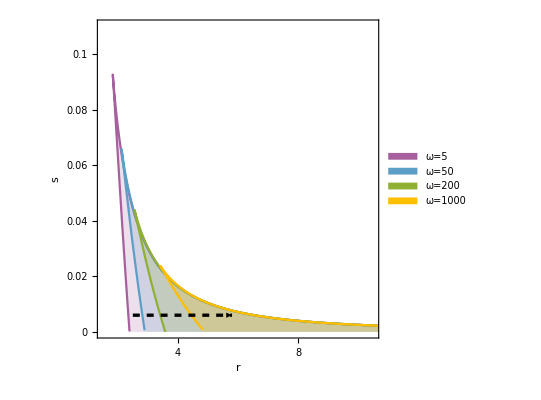

```mathematica
bistabilityOmega=ListLinePlot[{ddEsp5,ddEsp50,ddEsp200,ddEsp1000},PlotStyle->{ColorData[97,9],ColorData[97,7],ColorData[97,3],ColorData[97,8]},PlotLegends->Placed[SwatchLegend[{"ω=5","ω=50","ω=200","ω=1000"}],{Right,Top}],PlotRange->{{1.5,10.5},{0,0.11}},Filling->Bottom,Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["s",optsLabel1]},FrameTicks->{
{{{0,StyleForm["0",optsScale1],{0.03,0}},{0.02,StyleForm["0.02",optsScale1],{0.03,0}},{0.04,StyleForm["0.04",optsScale1],{0.03,0}},{0.06,StyleForm["0.06",optsScale1],{0.03,0}},{0.08,StyleForm["0.08",optsScale1],{0.03,0}},{0.1,StyleForm["0.1",optsScale1],{0.03,0}}},None},

{{{4,StyleForm["4",optsScale1],{0.03,0}},{6,StyleForm["6",optsScale1],{0.03,0}},{8,StyleForm["8",optsScale1],{0.03,0}},{10,StyleForm["10",optsScale1],{0.03,0}},{12,StyleForm["12",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}}},None}
},Epilog->{Dashed,Thickness[0.006],Arrow[{{2.5,0.006},{5.8,0.006}}]},AspectRatio->1]
```

Now we change p, with fixed ω=130

```mathematica
α=√(1600/5.6)
ω=130
```

16.9031

130

```mathematica
p=1.
```

1.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.278,0.002}]
```

{{250.181,3.99612×10^-6,0.002},{125.185,0.0000159682,0.004},{83.5228,0.0000358903,0.006},{62.6935,0.0000637339,0.008},{50.1976,0.0000994686,0.01},{41.8684,0.000143061,0.012},{35.9203,0.000194476,0.014},{31.4602,0.000253675,0.016},{27.9924,0.000320618,0.018},{25.219,0.000395259,0.02},{22.9508,0.000477553,0.022},{21.0615,0.000567448,0.024},{19.4637,0.000664889,0.026},{18.0949,0.000769819,0.028},{16.9095,0.000882174,0.03},{15.8729,0.00100189,0.032},{14.9591,0.00112889,0.034},{14.1476,0.00126309,0.036},{13.4223,0.00140442,0.038},{12.7702,0.00155279,0.04},{12.181,0.00170809,0.042},{11.6461,0.00187022,0.044},{11.1584,0.00203908,0.046},{10.7122,0.00221455,0.048},{10.3024,0.00239648,0.05},{9.9249,0.00258476,0.052},{9.57615,0.00277924,0.054},{9.25311,0.00297975,0.056},{8.95314,0.00318613,0.058},{8.67398,0.00339821,0.06},{8.41366,0.0036158,0.062},{8.17044,0.00383869,0.064},{7.94281,0.00406667,0.066},{7.72944,0.00429953,0.068},{7.52914,0.00453701,0.07},{7.34086,0.00477887,0.072},{7.16367,0.00502483,0.074},{6.99673,0.00527463,0.076},{6.83929,0.00552795,0.078},{6.69069,0.00578449,0.08},{6.55031,0.00604392,0.082},{6.41763,0.0063059,0.084},{6.29213,0.00657007,0.086},{6.17337,0.00683604,0.088},{6.06096,0.00710342,0.09},{5.95451,0.00737182,0.092},{5.8537,0.00764078,0.094},{5.75822,0.00790988,0.096},{5.66778,0.00817865,0.098},{5.58214,0.00844661,0.1},{5.50107,0.00871327,0.102},{5.42434,0.00897811,0.104},{5.35176,0.00924061,0.106},{5.28316,0.00950022,0.108},{5.21836,0.00975638,0.11},{5.15723,0.0100085,0.112},{5.09962,0.010256,0.114},{5.0454,0.0104983,0.116},{4.99447,0.0107348,0.118},{4.94671,0.0109648,0.12},{4.90204,0.0111877,0.122},{4.86036,0.0114029,0.124},{4.82159,0.0116096,0.126},{4.78568,0.0118073,0.128},{4.75255,0.0119952,0.13},{4.72214,0.0121727,0.132},{4.69441,0.012339,0.134},{4.66932,0.0124935,0.136},{4.64682,0.0126356,0.138},{4.62689,0.0127644,0.14},{4.6095,0.0128794,0.142},{4.59463,0.0129797,0.144},{4.58226,0.0130649,0.146},{4.57239,0.0131341,0.148},{4.56501,0.0131868,0.15},{4.56012,0.0132222,0.152},{4.55773,0.0132398,0.154},{4.55786,0.0132389,0.156},{4.5605,0.0132188,0.158},{4.5657,0.0131791,0.16},{4.57348,0.0131192,0.162},{4.58386,0.0130384,0.164},{4.5969,0.0129363,0.166},{4.61263,0.0128124,0.168},{4.6311,0.0126662,0.17},{4.65238,0.0124973,0.172},{4.67653,0.0123053,0.174},{4.70362,0.0120897,0.176},{4.73373,0.0118503,0.178},{4.76695,0.0115868,0.18},{4.80337,0.0112989,0.182},{4.8431,0.0109863,0.184},{4.88626,0.0106489,0.186},{4.93296,0.0102866,0.188},{4.98335,0.0098992,0.19},{5.03756,0.00948668,0.192},{5.09577,0.00904902,0.194},{5.15815,0.00858625,0.196},{5.22488,0.00809844,0.198},{5.29618,0.00758571,0.2},{5.37226,0.00704821,0.202},{5.45337,0.00648616,0.204},{5.53978,0.00589979,0.206},{5.63177,0.00528941,0.208},{5.72967,0.00465535,0.21},{5.8338,0.00399799,0.212},{5.94455,0.00331774,0.214},{6.06233,0.00261506,0.216},{6.18759,0.00189047,0.218},{6.32081,0.00114449,0.22},{6.46253,0.000377698,0.222},{6.61336,-0.000409293,0.224},{6.77395,-0.00121584,0.226},{6.94501,-0.00204126,0.228},{7.12736,-0.00288486,0.23},{7.32188,-0.00374589,0.232},{7.52955,-0.0046236,0.234},{7.75148,-0.00551719,0.236},{7.98891,-0.00642587,0.238},{8.24321,-0.00734879,0.24},{8.51594,-0.00828511,0.242},{8.80886,-0.00923397,0.244},{9.12396,-0.0101945,0.246},{9.4635,-0.0111658,0.248},{9.83006,-0.012147,0.25},{10.2266,-0.0131371,0.252},{10.6566,-0.0141353,0.254},{11.1239,-0.0151406,0.256},{11.6333,-0.0161521,0.258},{12.1901,-0.017169,0.26},{12.8006,-0.0181903,0.262},{13.4726,-0.019215,0.264},{14.2151,-0.0202424,0.266},{15.039,-0.0212714,0.268},{15.9578,-0.0223013,0.27},{16.988,-0.0233311,0.272},{18.1501,-0.0243601,0.274},{19.4701,-0.0253873,0.276},{20.9812,-0.0264119,0.278}}

```mathematica
ddEspp1=Table[{cc[[i,1]],cc[[i,2]]},{i,1,139,1}]
```

{{250.181,3.99612×10^-6},{125.185,0.0000159682},{83.5228,0.0000358903},{62.6935,0.0000637339},{50.1976,0.0000994686},{41.8684,0.000143061},{35.9203,0.000194476},{31.4602,0.000253675},{27.9924,0.000320618},{25.219,0.000395259},{22.9508,0.000477553},{21.0615,0.000567448},{19.4637,0.000664889},{18.0949,0.000769819},{16.9095,0.000882174},{15.8729,0.00100189},{14.9591,0.00112889},{14.1476,0.00126309},{13.4223,0.00140442},{12.7702,0.00155279},{12.181,0.00170809},{11.6461,0.00187022},{11.1584,0.00203908},{10.7122,0.00221455},{10.3024,0.00239648},{9.9249,0.00258476},{9.57615,0.00277924},{9.25311,0.00297975},{8.95314,0.00318613},{8.67398,0.00339821},{8.41366,0.0036158},{8.17044,0.00383869},{7.94281,0.00406667},{7.72944,0.00429953},{7.52914,0.00453701},{7.34086,0.00477887},{7.16367,0.00502483},{6.99673,0.00527463},{6.83929,0.00552795},{6.69069,0.00578449},{6.55031,0.00604392},{6.41763,0.0063059},{6.29213,0.00657007},{6.17337,0.00683604},{6.06096,0.00710342},{5.95451,0.00737182},{5.8537,0.00764078},{5.75822,0.00790988},{5.66778,0.00817865},{5.58214,0.00844661},{5.50107,0.00871327},{5.42434,0.00897811},{5.35176,0.00924061},{5.28316,0.00950022},{5.21836,0.00975638},{5.15723,0.0100085},{5.09962,0.010256},{5.0454,0.0104983},{4.99447,0.0107348},{4.94671,0.0109648},{4.90204,0.0111877},{4.86036,0.0114029},{4.82159,0.0116096},{4.78568,0.0118073},{4.75255,0.0119952},{4.72214,0.0121727},{4.69441,0.012339},{4.66932,0.0124935},{4.64682,0.0126356},{4.62689,0.0127644},{4.6095,0.0128794},{4.59463,0.0129797},{4.58226,0.0130649},{4.57239,0.0131341},{4.56501,0.0131868},{4.56012,0.0132222},{4.55773,0.0132398},{4.55786,0.0132389},{4.5605,0.0132188},{4.5657,0.0131791},{4.57348,0.0131192},{4.58386,0.0130384},{4.5969,0.0129363},{4.61263,0.0128124},{4.6311,0.0126662},{4.65238,0.0124973},{4.67653,0.0123053},{4.70362,0.0120897},{4.73373,0.0118503},{4.76695,0.0115868},{4.80337,0.0112989},{4.8431,0.0109863},{4.88626,0.0106489},{4.93296,0.0102866},{4.98335,0.0098992},{5.03756,0.00948668},{5.09577,0.00904902},{5.15815,0.00858625},{5.22488,0.00809844},{5.29618,0.00758571},{5.37226,0.00704821},{5.45337,0.00648616},{5.53978,0.00589979},{5.63177,0.00528941},{5.72967,0.00465535},{5.8338,0.00399799},{5.94455,0.00331774},{6.06233,0.00261506},{6.18759,0.00189047},{6.32081,0.00114449},{6.46253,0.000377698},{6.61336,-0.000409293},{6.77395,-0.00121584},{6.94501,-0.00204126},{7.12736,-0.00288486},{7.32188,-0.00374589},{7.52955,-0.0046236},{7.75148,-0.00551719},{7.98891,-0.00642587},{8.24321,-0.00734879},{8.51594,-0.00828511},{8.80886,-0.00923397},{9.12396,-0.0101945},{9.4635,-0.0111658},{9.83006,-0.012147},{10.2266,-0.0131371},{10.6566,-0.0141353},{11.1239,-0.0151406},{11.6333,-0.0161521},{12.1901,-0.017169},{12.8006,-0.0181903},{13.4726,-0.019215},{14.2151,-0.0202424},{15.039,-0.0212714},{15.9578,-0.0223013},{16.988,-0.0233311},{18.1501,-0.0243601},{19.4701,-0.0253873},{20.9812,-0.0264119}}

```mathematica
p=5.
```

5.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.414,0.002}]
```

{{250.18,3.99616×10^-6,0.002},{125.182,0.0000159688,0.004},{83.518,0.0000358934,0.006},{62.6871,0.0000637438,0.008},{50.1895,0.0000994929,0.01},{41.8586,0.000143112,0.012},{35.9086,0.000194571,0.014},{31.4468,0.000253839,0.016},{27.977,0.000320884,0.018},{25.2017,0.00039567,0.02},{22.9315,0.000478164,0.022},{21.0401,0.000568327,0.024},{19.4401,0.000666121,0.026},{18.069,0.000771506,0.028},{16.8811,0.00088444,0.03},{15.8421,0.00100488,0.032},{14.9256,0.00113278,0.034},{14.1114,0.0012681,0.036},{13.3831,0.00141077,0.038},{12.728,0.00156077,0.04},{12.1355,0.00171802,0.042},{11.5973,0.00188248,0.044},{11.1061,0.00205408,0.046},{10.6561,0.00223277,0.048},{10.2424,0.00241849,0.05},{9.86086,0.00261117,0.052},{9.50782,0.00281074,0.054},{9.18027,0.00301714,0.056},{8.87558,0.00323028,0.058},{8.59148,0.0034501,0.06},{8.32597,0.00367651,0.062},{8.07732,0.00390944,0.064},{7.84401,0.00414879,0.066},{7.62469,0.00439448,0.068},{7.41817,0.00464642,0.07},{7.22339,0.00490451,0.072},{7.0394,0.00516864,0.074},{6.86537,0.00543872,0.076},{6.70053,0.00571464,0.078},{6.5442,0.00599628,0.08},{6.39576,0.00628353,0.082},{6.25467,0.00657627,0.084},{6.12042,0.00687437,0.086},{5.99254,0.0071777,0.088},{5.87062,0.00748613,0.09},{5.75428,0.00779953,0.092},{5.64317,0.00811773,0.094},{5.53698,0.0084406,0.096},{5.4354,0.00876798,0.098},{5.33817,0.00909971,0.1},{5.24505,0.00943563,0.102},{5.1558,0.00977555,0.104},{5.07022,0.0101193,0.106},{4.9881,0.0104667,0.108},{4.90927,0.0108176,0.11},{4.83356,0.0111718,0.112},{4.76081,0.011529,0.114},{4.69088,0.0118891,0.116},{4.62364,0.0122518,0.118},{4.55895,0.012617,0.12},{4.49671,0.0129844,0.122},{4.4368,0.0133538,0.124},{4.37911,0.0137249,0.126},{4.32356,0.0140975,0.128},{4.27006,0.0144713,0.13},{4.21851,0.0148462,0.132},{4.16885,0.0152217,0.134},{4.121,0.0155978,0.136},{4.07488,0.015974,0.138},{4.03044,0.0163501,0.14},{3.98762,0.0167258,0.142},{3.94634,0.0171008,0.144},{3.90657,0.0174749,0.146},{3.86825,0.0178477,0.148},{3.83133,0.0182188,0.15},{3.79577,0.0185881,0.152},{3.76152,0.018955,0.154},{3.72855,0.0193195,0.156},{3.69681,0.0196809,0.158},{3.66628,0.0200392,0.16},{3.63691,0.0203938,0.162},{3.60867,0.0207444,0.164},{3.58154,0.0210908,0.166},{3.55549,0.0214324,0.168},{3.53049,0.021769,0.17},{3.50651,0.0221002,0.172},{3.48353,0.0224256,0.174},{3.46154,0.0227448,0.176},{3.4405,0.0230574,0.178},{3.42041,0.0233631,0.18},{3.40123,0.0236614,0.182},{3.38296,0.023952,0.184},{3.36558,0.0242345,0.186},{3.34907,0.0245084,0.188},{3.33342,0.0247733,0.19},{3.31861,0.025029,0.192},{3.30464,0.0252748,0.194},{3.29149,0.0255106,0.196},{3.27915,0.0257357,0.198},{3.26762,0.0259499,0.2},{3.25688,0.0261527,0.202},{3.24693,0.0263438,0.204},{3.23775,0.0265226,0.206},{3.22935,0.0266889,0.208},{3.22172,0.0268422,0.21},{3.21485,0.0269821,0.212},{3.20874,0.0271082,0.214},{3.20339,0.0272202,0.216},{3.19879,0.0273176,0.218},{3.19495,0.0274,0.22},{3.19185,0.0274671,0.222},{3.1895,0.0275185,0.224},{3.18791,0.0275538,0.226},{3.18706,0.0275726,0.228},{3.18697,0.0275747,0.23},{3.18763,0.0275596,0.232},{3.18906,0.027527,0.234},{3.19124,0.0274766,0.236},{3.19419,0.027408,0.238},{3.19791,0.0273209,0.24},{3.20241,0.0272151,0.242},{3.20769,0.0270901,0.244},{3.21376,0.0269458,0.246},{3.22063,0.0267819,0.248},{3.22831,0.026598,0.25},{3.2368,0.0263939,0.252},{3.24613,0.0261694,0.254},{3.25629,0.0259242,0.256},{3.2673,0.0256582,0.258},{3.27918,0.0253711,0.26},{3.29193,0.0250627,0.262},{3.30558,0.0247328,0.264},{3.32014,0.0243813,0.266},{3.33562,0.0240081,0.268},{3.35204,0.0236129,0.27},{3.36943,0.0231957,0.272},{3.3878,0.0227564,0.274},{3.40717,0.0222948,0.276},{3.42757,0.0218109,0.278},{3.44902,0.0213047,0.28},{3.47155,0.020776,0.282},{3.49517,0.020225,0.284},{3.51993,0.0196514,0.286},{3.54585,0.0190554,0.288},{3.57296,0.018437,0.29},{3.60129,0.0177963,0.292},{3.63088,0.0171331,0.294},{3.66177,0.0164478,0.296},{3.694,0.0157402,0.298},{3.7276,0.0150106,0.3},{3.76262,0.0142591,0.302},{3.7991,0.0134857,0.304},{3.8371,0.0126907,0.306},{3.87666,0.0118742,0.308},{3.91784,0.0110364,0.31},{3.96069,0.0101776,0.312},{4.00528,0.0092978,0.314},{4.05166,0.0083974,0.316},{4.09992,0.0074766,0.318},{4.1501,0.00653568,0.32},{4.2023,0.0055749,0.322},{4.25659,0.00459456,0.324},{4.31306,0.00359496,0.326},{4.37179,0.00257644,0.328},{4.43288,0.00153931,0.33},{4.49643,0.00048393,0.332},{4.56255,-0.000589342,0.334},{4.63136,-0.00168013,0.336},{4.70296,-0.00278806,0.338},{4.77751,-0.00391273,0.34},{4.85512,-0.00505374,0.342},{4.93595,-0.00621067,0.344},{5.02016,-0.00738308,0.346},{5.10791,-0.00857056,0.348},{5.19938,-0.00977264,0.35},{5.29478,-0.0109889,0.352},{5.39429,-0.0122188,0.354},{5.49815,-0.013462,0.356},{5.60659,-0.0147179,0.358},{5.71988,-0.015986,0.36},{5.83828,-0.017266,0.362},{5.96209,-0.0185572,0.364},{6.09165,-0.0198592,0.366},{6.22729,-0.0211715,0.368},{6.3694,-0.0224935,0.37},{6.51838,-0.0238248,0.372},{6.67469,-0.0251648,0.374},{6.8388,-0.0265131,0.376},{7.01126,-0.0278691,0.378},{7.19264,-0.0292322,0.38},{7.38357,-0.030602,0.382},{7.58477,-0.031978,0.384},{7.79698,-0.0333595,0.386},{8.02107,-0.0347462,0.388},{8.25797,-0.0361374,0.39},{8.50871,-0.0375327,0.392},{8.77445,-0.0389315,0.394},{9.05648,-0.0403334,0.396},{9.35622,-0.0417378,0.398},{9.6753,-0.0431442,0.4},{10.0155,-0.0445521,0.402},{10.3789,-0.045961,0.404},{10.7679,-0.0473704,0.406},{11.1849,-0.0487798,0.408},{11.6332,-0.0501888,0.41},{12.1161,-0.0515968,0.412},{12.6375,-0.0530034,0.414}}

```mathematica
ddEspp5=Table[{cc[[i,1]],cc[[i,2]]},{i,1,207,1}]
```

{{250.18,3.99616×10^-6},{125.182,0.0000159688},{83.518,0.0000358934},{62.6871,0.0000637438},{50.1895,0.0000994929},{41.8586,0.000143112},{35.9086,0.000194571},{31.4468,0.000253839},{27.977,0.000320884},{25.2017,0.00039567},{22.9315,0.000478164},{21.0401,0.000568327},{19.4401,0.000666121},{18.069,0.000771506},{16.8811,0.00088444},{15.8421,0.00100488},{14.9256,0.00113278},{14.1114,0.0012681},{13.3831,0.00141077},{12.728,0.00156077},{12.1355,0.00171802},{11.5973,0.00188248},{11.1061,0.00205408},{10.6561,0.00223277},{10.2424,0.00241849},{9.86086,0.00261117},{9.50782,0.00281074},{9.18027,0.00301714},{8.87558,0.00323028},{8.59148,0.0034501},{8.32597,0.00367651},{8.07732,0.00390944},{7.84401,0.00414879},{7.62469,0.00439448},{7.41817,0.00464642},{7.22339,0.00490451},{7.0394,0.00516864},{6.86537,0.00543872},{6.70053,0.00571464},{6.5442,0.00599628},{6.39576,0.00628353},{6.25467,0.00657627},{6.12042,0.00687437},{5.99254,0.0071777},{5.87062,0.00748613},{5.75428,0.00779953},{5.64317,0.00811773},{5.53698,0.0084406},{5.4354,0.00876798},{5.33817,0.00909971},{5.24505,0.00943563},{5.1558,0.00977555},{5.07022,0.0101193},{4.9881,0.0104667},{4.90927,0.0108176},{4.83356,0.0111718},{4.76081,0.011529},{4.69088,0.0118891},{4.62364,0.0122518},{4.55895,0.012617},{4.49671,0.0129844},{4.4368,0.0133538},{4.37911,0.0137249},{4.32356,0.0140975},{4.27006,0.0144713},{4.21851,0.0148462},{4.16885,0.0152217},{4.121,0.0155978},{4.07488,0.015974},{4.03044,0.0163501},{3.98762,0.0167258},{3.94634,0.0171008},{3.90657,0.0174749},{3.86825,0.0178477},{3.83133,0.0182188},{3.79577,0.0185881},{3.76152,0.018955},{3.72855,0.0193195},{3.69681,0.0196809},{3.66628,0.0200392},{3.63691,0.0203938},{3.60867,0.0207444},{3.58154,0.0210908},{3.55549,0.0214324},{3.53049,0.021769},{3.50651,0.0221002},{3.48353,0.0224256},{3.46154,0.0227448},{3.4405,0.0230574},{3.42041,0.0233631},{3.40123,0.0236614},{3.38296,0.023952},{3.36558,0.0242345},{3.34907,0.0245084},{3.33342,0.0247733},{3.31861,0.025029},{3.30464,0.0252748},{3.29149,0.0255106},{3.27915,0.0257357},{3.26762,0.0259499},{3.25688,0.0261527},{3.24693,0.0263438},{3.23775,0.0265226},{3.22935,0.0266889},{3.22172,0.0268422},{3.21485,0.0269821},{3.20874,0.0271082},{3.20339,0.0272202},{3.19879,0.0273176},{3.19495,0.0274},{3.19185,0.0274671},{3.1895,0.0275185},{3.18791,0.0275538},{3.18706,0.0275726},{3.18697,0.0275747},{3.18763,0.0275596},{3.18906,0.027527},{3.19124,0.0274766},{3.19419,0.027408},{3.19791,0.0273209},{3.20241,0.0272151},{3.20769,0.0270901},{3.21376,0.0269458},{3.22063,0.0267819},{3.22831,0.026598},{3.2368,0.0263939},{3.24613,0.0261694},{3.25629,0.0259242},{3.2673,0.0256582},{3.27918,0.0253711},{3.29193,0.0250627},{3.30558,0.0247328},{3.32014,0.0243813},{3.33562,0.0240081},{3.35204,0.0236129},{3.36943,0.0231957},{3.3878,0.0227564},{3.40717,0.0222948},{3.42757,0.0218109},{3.44902,0.0213047},{3.47155,0.020776},{3.49517,0.020225},{3.51993,0.0196514},{3.54585,0.0190554},{3.57296,0.018437},{3.60129,0.0177963},{3.63088,0.0171331},{3.66177,0.0164478},{3.694,0.0157402},{3.7276,0.0150106},{3.76262,0.0142591},{3.7991,0.0134857},{3.8371,0.0126907},{3.87666,0.0118742},{3.91784,0.0110364},{3.96069,0.0101776},{4.00528,0.0092978},{4.05166,0.0083974},{4.09992,0.0074766},{4.1501,0.00653568},{4.2023,0.0055749},{4.25659,0.00459456},{4.31306,0.00359496},{4.37179,0.00257644},{4.43288,0.00153931},{4.49643,0.00048393},{4.56255,-0.000589342},{4.63136,-0.00168013},{4.70296,-0.00278806},{4.77751,-0.00391273},{4.85512,-0.00505374},{4.93595,-0.00621067},{5.02016,-0.00738308},{5.10791,-0.00857056},{5.19938,-0.00977264},{5.29478,-0.0109889},{5.39429,-0.0122188},{5.49815,-0.013462},{5.60659,-0.0147179},{5.71988,-0.015986},{5.83828,-0.017266},{5.96209,-0.0185572},{6.09165,-0.0198592},{6.22729,-0.0211715},{6.3694,-0.0224935},{6.51838,-0.0238248},{6.67469,-0.0251648},{6.8388,-0.0265131},{7.01126,-0.0278691},{7.19264,-0.0292322},{7.38357,-0.030602},{7.58477,-0.031978},{7.79698,-0.0333595},{8.02107,-0.0347462},{8.25797,-0.0361374},{8.50871,-0.0375327},{8.77445,-0.0389315},{9.05648,-0.0403334},{9.35622,-0.0417378},{9.6753,-0.0431442},{10.0155,-0.0445521},{10.3789,-0.045961},{10.7679,-0.0473704},{11.1849,-0.0487798},{11.6332,-0.0501888},{12.1161,-0.0515968},{12.6375,-0.0530034}}

```mathematica
p=50.
```

50.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.68,0.002}]
```

{{250.18,3.99617×10^-6,0.002},{125.182,0.000015969,0.004},{83.5169,0.0000358941,0.006},{62.6856,0.0000637461,0.008},{50.1876,0.0000994984,0.01},{41.8563,0.000143123,0.012},{35.906,0.000194593,0.014},{31.4437,0.000253876,0.016},{27.9736,0.000320944,0.018},{25.1978,0.000395763,0.02},{22.9271,0.000478301,0.022},{21.0353,0.000568525,0.024},{19.4347,0.000666398,0.026},{18.0632,0.000771886,0.028},{16.8748,0.000884951,0.03},{15.8352,0.00100556,0.032},{14.9181,0.00113366,0.034},{14.1032,0.00126922,0.036},{13.3743,0.00141221,0.038},{12.7185,0.00156257,0.04},{12.1253,0.00172026,0.042},{11.5863,0.00188524,0.044},{11.0943,0.00205747,0.046},{10.6435,0.0022369,0.048},{10.229,0.00242347,0.05},{9.84649,0.00261715,0.052},{9.49249,0.00281788,0.054},{9.16393,0.00302561,0.056},{8.85819,0.0032403,0.058},{8.57298,0.00346188,0.06},{8.30632,0.00369031,0.062},{8.05646,0.00392553,0.064},{7.82189,0.00416748,0.066},{7.60125,0.00441611,0.068},{7.39335,0.00467137,0.07},{7.19713,0.00493318,0.072},{7.01165,0.0052015,0.074},{6.83605,0.00547626,0.076},{6.66958,0.0057574,0.078},{6.51155,0.00604486,0.08},{6.36135,0.00633857,0.082},{6.21842,0.00663847,0.084},{6.08225,0.00694449,0.086},{5.95238,0.00725656,0.088},{5.8284,0.00757463,0.09},{5.70991,0.00789861,0.092},{5.59658,0.00822843,0.094},{5.48808,0.00856403,0.096},{5.38411,0.00890534,0.098},{5.2844,0.00925228,0.1},{5.18871,0.00960477,0.102},{5.09679,0.00996274,0.104},{5.00845,0.0103261,0.106},{4.92348,0.0106948,0.108},{4.8417,0.0110687,0.11},{4.76294,0.0114478,0.112},{4.68704,0.011832,0.114},{4.61385,0.0122212,0.116},{4.54325,0.0126153,0.118},{4.47509,0.0130143,0.12},{4.40925,0.013418,0.122},{4.34564,0.0138263,0.124},{4.28414,0.0142392,0.126},{4.22466,0.0146566,0.128},{4.16709,0.0150784,0.13},{4.11137,0.0155045,0.132},{4.0574,0.0159348,0.134},{4.0051,0.0163692,0.136},{3.95442,0.0168077,0.138},{3.90527,0.0172501,0.14},{3.8576,0.0176962,0.142},{3.81134,0.0181462,0.144},{3.76644,0.0185997,0.146},{3.72284,0.0190568,0.148},{3.68049,0.0195173,0.15},{3.63934,0.0199811,0.152},{3.59936,0.0204482,0.154},{3.56048,0.0209183,0.156},{3.52268,0.0213915,0.158},{3.48591,0.0218676,0.16},{3.45014,0.0223465,0.162},{3.41533,0.022828,0.164},{3.38144,0.0233122,0.166},{3.34845,0.0237987,0.168},{3.31632,0.0242877,0.17},{3.28503,0.0247789,0.172},{3.25455,0.0252722,0.174},{3.22484,0.0257675,0.176},{3.19589,0.0262647,0.178},{3.16767,0.0267636,0.18},{3.14016,0.0272642,0.182},{3.11333,0.0277664,0.184},{3.08717,0.0282699,0.186},{3.06166,0.0287747,0.188},{3.03676,0.0292807,0.19},{3.01248,0.0297878,0.192},{2.98878,0.0302957,0.194},{2.96566,0.0308044,0.196},{2.94309,0.0313138,0.198},{2.92106,0.0318237,0.2},{2.89956,0.032334,0.202},{2.87856,0.0328446,0.204},{2.85807,0.0333553,0.206},{2.83806,0.033866,0.208},{2.81851,0.0343766,0.21},{2.79943,0.034887,0.212},{2.78079,0.0353969,0.214},{2.76259,0.0359063,0.216},{2.74481,0.036415,0.218},{2.72745,0.036923,0.22},{2.71049,0.0374299,0.222},{2.69393,0.0379358,0.224},{2.67775,0.0384405,0.226},{2.66194,0.0389438,0.228},{2.6465,0.0394456,0.23},{2.63143,0.0399457,0.232},{2.6167,0.0404441,0.234},{2.60231,0.0409405,0.236},{2.58827,0.0414348,0.238},{2.57455,0.0419269,0.24},{2.56115,0.0424167,0.242},{2.54806,0.0429039,0.244},{2.53528,0.0433885,0.246},{2.52281,0.0438702,0.248},{2.51063,0.044349,0.25},{2.49874,0.0448247,0.252},{2.48714,0.0452971,0.254},{2.47581,0.0457661,0.256},{2.46476,0.0462316,0.258},{2.45398,0.0466933,0.26},{2.44346,0.0471512,0.262},{2.43319,0.0476051,0.264},{2.42319,0.0480548,0.266},{2.41343,0.0485003,0.268},{2.40392,0.0489413,0.27},{2.39465,0.0493776,0.272},{2.38562,0.0498092,0.274},{2.37682,0.0502359,0.276},{2.36825,0.0506575,0.278},{2.35991,0.0510739,0.28},{2.35179,0.051485,0.282},{2.3439,0.0518905,0.284},{2.33621,0.0522903,0.286},{2.32874,0.0526843,0.288},{2.32149,0.0530723,0.29},{2.31443,0.0534543,0.292},{2.30759,0.0538299,0.294},{2.30094,0.0541991,0.296},{2.2945,0.0545617,0.298},{2.28825,0.0549175,0.3},{2.28219,0.0552665,0.302},{2.27633,0.0556085,0.304},{2.27066,0.0559432,0.306},{2.26517,0.0562707,0.308},{2.25987,0.0565906,0.31},{2.25475,0.0569029,0.312},{2.24982,0.0572075,0.314},{2.24506,0.0575041,0.316},{2.24048,0.0577926,0.318},{2.23608,0.0580729,0.32},{2.23185,0.0583449,0.322},{2.2278,0.0586083,0.324},{2.22391,0.0588631,0.326},{2.2202,0.0591091,0.328},{2.21665,0.0593462,0.33},{2.21327,0.0595742,0.332},{2.21006,0.059793,0.334},{2.20701,0.0600024,0.336},{2.20412,0.0602023,0.338},{2.2014,0.0603926,0.34},{2.19884,0.0605731,0.342},{2.19643,0.0607437,0.344},{2.19419,0.0609043,0.346},{2.19211,0.0610547,0.348},{2.19018,0.0611948,0.35},{2.18841,0.0613245,0.352},{2.18679,0.0614437,0.354},{2.18533,0.0615521,0.356},{2.18403,0.0616498,0.358},{2.18288,0.0617365,0.36},{2.18188,0.0618121,0.362},{2.18103,0.0618766,0.364},{2.18034,0.0619298,0.366},{2.1798,0.0619715,0.368},{2.17941,0.0620018,0.37},{2.17917,0.0620204,0.372},{2.17908,0.0620272,0.374},{2.17915,0.0620222,0.376},{2.17936,0.0620052,0.378},{2.17972,0.0619761,0.38},{2.18024,0.0619349,0.382},{2.1809,0.0618813,0.384},{2.18172,0.0618153,0.386},{2.18268,0.0617369,0.388},{2.1838,0.0616459,0.39},{2.18507,0.0615421,0.392},{2.18648,0.0614256,0.394},{2.18805,0.0612963,0.396},{2.18977,0.0611539,0.398},{2.19164,0.0609986,0.4},{2.19366,0.0608301,0.402},{2.19583,0.0606484,0.404},{2.19815,0.0604533,0.406},{2.20063,0.060245,0.408},{2.20326,0.0600232,0.41},{2.20604,0.0597878,0.412},{2.20898,0.0595389,0.414},{2.21207,0.0592763,0.416},{2.21532,0.059,0.418},{2.21872,0.0587099,0.42},{2.22228,0.058406,0.422},{2.226,0.0580881,0.424},{2.22987,0.0577563,0.426},{2.2339,0.0574105,0.428},{2.2381,0.0570506,0.43},{2.24245,0.0566766,0.432},{2.24697,0.0562885,0.434},{2.25165,0.0558861,0.436},{2.25649,0.0554695,0.438},{2.2615,0.0550386,0.44},{2.26668,0.0545934,0.442},{2.27202,0.0541339,0.444},{2.27753,0.05366,0.446},{2.28321,0.0531717,0.448},{2.28906,0.0526689,0.45},{2.29509,0.0521517,0.452},{2.30129,0.05162,0.454},{2.30766,0.0510739,0.456},{2.31421,0.0505132,0.458},{2.32094,0.0499381,0.46},{2.32785,0.0493484,0.462},{2.33495,0.0487442,0.464},{2.34222,0.0481255,0.466},{2.34969,0.0474922,0.468},{2.35734,0.0468445,0.47},{2.36518,0.0461822,0.472},{2.37321,0.0455054,0.474},{2.38143,0.0448141,0.476},{2.38985,0.0441084,0.478},{2.39847,0.0433882,0.48},{2.40729,0.0426535,0.482},{2.41631,0.0419044,0.484},{2.42554,0.041141,0.486},{2.43497,0.0403631,0.488},{2.44461,0.039571,0.49},{2.45447,0.0387645,0.492},{2.46454,0.0379437,0.494},{2.47483,0.0371088,0.496},{2.48534,0.0362596,0.498},{2.49607,0.0353963,0.5},{2.50703,0.0345189,0.502},{2.51822,0.0336275,0.504},{2.52964,0.0327221,0.506},{2.54129,0.0318027,0.508},{2.55319,0.0308695,0.51},{2.56533,0.0299225,0.512},{2.57771,0.0289616,0.514},{2.59035,0.0279871,0.516},{2.60324,0.026999,0.518},{2.61638,0.0259973,0.52},{2.62979,0.0249822,0.522},{2.64346,0.0239536,0.524},{2.6574,0.0229117,0.526},{2.67162,0.0218566,0.528},{2.68611,0.0207883,0.53},{2.70088,0.0197069,0.532},{2.71595,0.0186125,0.534},{2.7313,0.0175052,0.536},{2.74695,0.0163851,0.538},{2.7629,0.0152523,0.54},{2.77916,0.0141068,0.542},{2.79573,0.0129489,0.544},{2.81261,0.0117785,0.546},{2.82982,0.0105957,0.548},{2.84736,0.00940078,0.55},{2.86523,0.00819373,0.552},{2.88344,0.00697467,0.554},{2.902,0.00574372,0.556},{2.92092,0.00450099,0.558},{2.94019,0.00324659,0.56},{2.95982,0.00198064,0.562},{2.97984,0.000703259,0.564},{3.00023,-0.000585434,0.566},{3.02101,-0.00188532,0.568},{3.04218,-0.00319627,0.57},{3.06376,-0.00451816,0.572},{3.08575,-0.00585087,0.574},{3.10815,-0.00719426,0.576},{3.13099,-0.00854821,0.578},{3.15426,-0.00991259,0.58},{3.17798,-0.0112873,0.582},{3.20215,-0.0126721,0.584},{3.22679,-0.0140669,0.586},{3.2519,-0.0154717,0.588},{3.27749,-0.0168861,0.59},{3.30358,-0.0183102,0.592},{3.33018,-0.0197438,0.594},{3.35729,-0.0211867,0.596},{3.38493,-0.0226387,0.598},{3.41311,-0.0240998,0.6},{3.44185,-0.0255698,0.602},{3.47114,-0.0270485,0.604},{3.50102,-0.0285358,0.606},{3.53149,-0.0300315,0.608},{3.56256,-0.0315356,0.61},{3.59425,-0.0330478,0.612},{3.62657,-0.034568,0.614},{3.65955,-0.036096,0.616},{3.69319,-0.0376317,0.618},{3.72751,-0.039175,0.62},{3.76253,-0.0407256,0.622},{3.79827,-0.0422834,0.624},{3.83474,-0.0438484,0.626},{3.87196,-0.0454202,0.628},{3.90995,-0.0469988,0.63},{3.94874,-0.048584,0.632},{3.98834,-0.0501756,0.634},{4.02877,-0.0517735,0.636},{4.07006,-0.0533775,0.638},{4.11223,-0.0549875,0.64},{4.15531,-0.0566033,0.642},{4.19931,-0.0582248,0.644},{4.24426,-0.0598517,0.646},{4.2902,-0.061484,0.648},{4.33715,-0.0631214,0.65},{4.38513,-0.0647638,0.652},{4.43418,-0.0664111,0.654},{4.48433,-0.0680631,0.656},{4.53561,-0.0697196,0.658},{4.58806,-0.0713804,0.66},{4.64171,-0.0730455,0.662},{4.69659,-0.0747146,0.664},{4.75274,-0.0763876,0.666},{4.81022,-0.0780644,0.668},{4.86904,-0.0797447,0.67},{4.92927,-0.0814284,0.672},{4.99093,-0.0831153,0.674},{5.05409,-0.0848054,0.676},{5.11879,-0.0864984,0.678},{5.18507,-0.0881942,0.68}}

```mathematica
ddEspp50=Table[{cc[[i,1]],cc[[i,2]]},{i,1,340,1}]
```

{{250.18,3.99617×10^-6},{125.182,0.000015969},{83.5169,0.0000358941},{62.6856,0.0000637461},{50.1876,0.0000994984},{41.8563,0.000143123},{35.906,0.000194593},{31.4437,0.000253876},{27.9736,0.000320944},{25.1978,0.000395763},{22.9271,0.000478301},{21.0353,0.000568525},{19.4347,0.000666398},{18.0632,0.000771886},{16.8748,0.000884951},{15.8352,0.00100556},{14.9181,0.00113366},{14.1032,0.00126922},{13.3743,0.00141221},{12.7185,0.00156257},{12.1253,0.00172026},{11.5863,0.00188524},{11.0943,0.00205747},{10.6435,0.0022369},{10.229,0.00242347},{9.84649,0.00261715},{9.49249,0.00281788},{9.16393,0.00302561},{8.85819,0.0032403},{8.57298,0.00346188},{8.30632,0.00369031},{8.05646,0.00392553},{7.82189,0.00416748},{7.60125,0.00441611},{7.39335,0.00467137},{7.19713,0.00493318},{7.01165,0.0052015},{6.83605,0.00547626},{6.66958,0.0057574},{6.51155,0.00604486},{6.36135,0.00633857},{6.21842,0.00663847},{6.08225,0.00694449},{5.95238,0.00725656},{5.8284,0.00757463},{5.70991,0.00789861},{5.59658,0.00822843},{5.48808,0.00856403},{5.38411,0.00890534},{5.2844,0.00925228},{5.18871,0.00960477},{5.09679,0.00996274},{5.00845,0.0103261},{4.92348,0.0106948},{4.8417,0.0110687},{4.76294,0.0114478},{4.68704,0.011832},{4.61385,0.0122212},{4.54325,0.0126153},{4.47509,0.0130143},{4.40925,0.013418},{4.34564,0.0138263},{4.28414,0.0142392},{4.22466,0.0146566},{4.16709,0.0150784},{4.11137,0.0155045},{4.0574,0.0159348},{4.0051,0.0163692},{3.95442,0.0168077},{3.90527,0.0172501},{3.8576,0.0176962},{3.81134,0.0181462},{3.76644,0.0185997},{3.72284,0.0190568},{3.68049,0.0195173},{3.63934,0.0199811},{3.59936,0.0204482},{3.56048,0.0209183},{3.52268,0.0213915},{3.48591,0.0218676},{3.45014,0.0223465},{3.41533,0.022828},{3.38144,0.0233122},{3.34845,0.0237987},{3.31632,0.0242877},{3.28503,0.0247789},{3.25455,0.0252722},{3.22484,0.0257675},{3.19589,0.0262647},{3.16767,0.0267636},{3.14016,0.0272642},{3.11333,0.0277664},{3.08717,0.0282699},{3.06166,0.0287747},{3.03676,0.0292807},{3.01248,0.0297878},{2.98878,0.0302957},{2.96566,0.0308044},{2.94309,0.0313138},{2.92106,0.0318237},{2.89956,0.032334},{2.87856,0.0328446},{2.85807,0.0333553},{2.83806,0.033866},{2.81851,0.0343766},{2.79943,0.034887},{2.78079,0.0353969},{2.76259,0.0359063},{2.74481,0.036415},{2.72745,0.036923},{2.71049,0.0374299},{2.69393,0.0379358},{2.67775,0.0384405},{2.66194,0.0389438},{2.6465,0.0394456},{2.63143,0.0399457},{2.6167,0.0404441},{2.60231,0.0409405},{2.58827,0.0414348},{2.57455,0.0419269},{2.56115,0.0424167},{2.54806,0.0429039},{2.53528,0.0433885},{2.52281,0.0438702},{2.51063,0.044349},{2.49874,0.0448247},{2.48714,0.0452971},{2.47581,0.0457661},{2.46476,0.0462316},{2.45398,0.0466933},{2.44346,0.0471512},{2.43319,0.0476051},{2.42319,0.0480548},{2.41343,0.0485003},{2.40392,0.0489413},{2.39465,0.0493776},{2.38562,0.0498092},{2.37682,0.0502359},{2.36825,0.0506575},{2.35991,0.0510739},{2.35179,0.051485},{2.3439,0.0518905},{2.33621,0.0522903},{2.32874,0.0526843},{2.32149,0.0530723},{2.31443,0.0534543},{2.30759,0.0538299},{2.30094,0.0541991},{2.2945,0.0545617},{2.28825,0.0549175},{2.28219,0.0552665},{2.27633,0.0556085},{2.27066,0.0559432},{2.26517,0.0562707},{2.25987,0.0565906},{2.25475,0.0569029},{2.24982,0.0572075},{2.24506,0.0575041},{2.24048,0.0577926},{2.23608,0.0580729},{2.23185,0.0583449},{2.2278,0.0586083},{2.22391,0.0588631},{2.2202,0.0591091},{2.21665,0.0593462},{2.21327,0.0595742},{2.21006,0.059793},{2.20701,0.0600024},{2.20412,0.0602023},{2.2014,0.0603926},{2.19884,0.0605731},{2.19643,0.0607437},{2.19419,0.0609043},{2.19211,0.0610547},{2.19018,0.0611948},{2.18841,0.0613245},{2.18679,0.0614437},{2.18533,0.0615521},{2.18403,0.0616498},{2.18288,0.0617365},{2.18188,0.0618121},{2.18103,0.0618766},{2.18034,0.0619298},{2.1798,0.0619715},{2.17941,0.0620018},{2.17917,0.0620204},{2.17908,0.0620272},{2.17915,0.0620222},{2.17936,0.0620052},{2.17972,0.0619761},{2.18024,0.0619349},{2.1809,0.0618813},{2.18172,0.0618153},{2.18268,0.0617369},{2.1838,0.0616459},{2.18507,0.0615421},{2.18648,0.0614256},{2.18805,0.0612963},{2.18977,0.0611539},{2.19164,0.0609986},{2.19366,0.0608301},{2.19583,0.0606484},{2.19815,0.0604533},{2.20063,0.060245},{2.20326,0.0600232},{2.20604,0.0597878},{2.20898,0.0595389},{2.21207,0.0592763},{2.21532,0.059},{2.21872,0.0587099},{2.22228,0.058406},{2.226,0.0580881},{2.22987,0.0577563},{2.2339,0.0574105},{2.2381,0.0570506},{2.24245,0.0566766},{2.24697,0.0562885},{2.25165,0.0558861},{2.25649,0.0554695},{2.2615,0.0550386},{2.26668,0.0545934},{2.27202,0.0541339},{2.27753,0.05366},{2.28321,0.0531717},{2.28906,0.0526689},{2.29509,0.0521517},{2.30129,0.05162},{2.30766,0.0510739},{2.31421,0.0505132},{2.32094,0.0499381},{2.32785,0.0493484},{2.33495,0.0487442},{2.34222,0.0481255},{2.34969,0.0474922},{2.35734,0.0468445},{2.36518,0.0461822},{2.37321,0.0455054},{2.38143,0.0448141},{2.38985,0.0441084},{2.39847,0.0433882},{2.40729,0.0426535},{2.41631,0.0419044},{2.42554,0.041141},{2.43497,0.0403631},{2.44461,0.039571},{2.45447,0.0387645},{2.46454,0.0379437},{2.47483,0.0371088},{2.48534,0.0362596},{2.49607,0.0353963},{2.50703,0.0345189},{2.51822,0.0336275},{2.52964,0.0327221},{2.54129,0.0318027},{2.55319,0.0308695},{2.56533,0.0299225},{2.57771,0.0289616},{2.59035,0.0279871},{2.60324,0.026999},{2.61638,0.0259973},{2.62979,0.0249822},{2.64346,0.0239536},{2.6574,0.0229117},{2.67162,0.0218566},{2.68611,0.0207883},{2.70088,0.0197069},{2.71595,0.0186125},{2.7313,0.0175052},{2.74695,0.0163851},{2.7629,0.0152523},{2.77916,0.0141068},{2.79573,0.0129489},{2.81261,0.0117785},{2.82982,0.0105957},{2.84736,0.00940078},{2.86523,0.00819373},{2.88344,0.00697467},{2.902,0.00574372},{2.92092,0.00450099},{2.94019,0.00324659},{2.95982,0.00198064},{2.97984,0.000703259},{3.00023,-0.000585434},{3.02101,-0.00188532},{3.04218,-0.00319627},{3.06376,-0.00451816},{3.08575,-0.00585087},{3.10815,-0.00719426},{3.13099,-0.00854821},{3.15426,-0.00991259},{3.17798,-0.0112873},{3.20215,-0.0126721},{3.22679,-0.0140669},{3.2519,-0.0154717},{3.27749,-0.0168861},{3.30358,-0.0183102},{3.33018,-0.0197438},{3.35729,-0.0211867},{3.38493,-0.0226387},{3.41311,-0.0240998},{3.44185,-0.0255698},{3.47114,-0.0270485},{3.50102,-0.0285358},{3.53149,-0.0300315},{3.56256,-0.0315356},{3.59425,-0.0330478},{3.62657,-0.034568},{3.65955,-0.036096},{3.69319,-0.0376317},{3.72751,-0.039175},{3.76253,-0.0407256},{3.79827,-0.0422834},{3.83474,-0.0438484},{3.87196,-0.0454202},{3.90995,-0.0469988},{3.94874,-0.048584},{3.98834,-0.0501756},{4.02877,-0.0517735},{4.07006,-0.0533775},{4.11223,-0.0549875},{4.15531,-0.0566033},{4.19931,-0.0582248},{4.24426,-0.0598517},{4.2902,-0.061484},{4.33715,-0.0631214},{4.38513,-0.0647638},{4.43418,-0.0664111},{4.48433,-0.0680631},{4.53561,-0.0697196},{4.58806,-0.0713804},{4.64171,-0.0730455},{4.69659,-0.0747146},{4.75274,-0.0763876},{4.81022,-0.0780644},{4.86904,-0.0797447},{4.92927,-0.0814284},{4.99093,-0.0831153},{5.05409,-0.0848054},{5.11879,-0.0864984},{5.18507,-0.0881942}}

```mathematica
p=500.
```

500.

```mathematica
cc=Table[{r,s,ct},{ct,0.002,0.916,0.002}]
```

{{250.179,3.99617×10^-6,0.002},{125.181,0.000015969,0.004},{83.5168,0.0000358942,0.006},{62.6855,0.0000637463,0.008},{50.1874,0.0000994989,0.01},{41.8561,0.000143125,0.012},{35.9057,0.000194595,0.014},{31.4434,0.00025388,0.016},{27.9732,0.00032095,0.018},{25.1974,0.000395772,0.02},{22.9267,0.000478315,0.022},{21.0348,0.000568545,0.024},{19.4342,0.000666426,0.026},{18.0626,0.000771924,0.028},{16.8741,0.000885002,0.03},{15.8345,0.00100562,0.032},{14.9174,0.00113375,0.034},{14.1024,0.00126934,0.036},{13.3734,0.00141235,0.038},{12.7175,0.00156275,0.04},{12.1243,0.00172049,0.042},{11.5852,0.00188552,0.044},{11.0932,0.00205781,0.046},{10.6423,0.00223731,0.048},{10.2276,0.00242397,0.05},{9.84505,0.00261775,0.052},{9.49096,0.00281859,0.054},{9.1623,0.00302646,0.056},{8.85645,0.0032413,0.058},{8.57113,0.00346306,0.06},{8.30436,0.00369169,0.062},{8.05438,0.00392714,0.064},{7.81968,0.00416935,0.066},{7.59891,0.00441828,0.068},{7.39087,0.00467387,0.07},{7.19451,0.00493606,0.072},{7.00888,0.0052048,0.074},{6.83312,0.00548003,0.076},{6.66649,0.00576169,0.078},{6.50829,0.00604973,0.08},{6.35792,0.0063441,0.082},{6.2148,0.00664471,0.084},{6.07844,0.00695153,0.086},{5.94838,0.00726449,0.088},{5.82419,0.00758352,0.09},{5.70549,0.00790857,0.092},{5.59194,0.00823957,0.094},{5.4832,0.00857646,0.096},{5.379,0.00891918,0.098},{5.27904,0.00926765,0.1},{5.1831,0.00962182,0.102},{5.09092,0.00998162,0.104},{5.00231,0.010347,0.106},{4.91706,0.0107178,0.108},{4.83498,0.0110941,0.11},{4.75592,0.0114758,0.112},{4.67971,0.0118627,0.114},{4.60621,0.0122549,0.116},{4.53527,0.0126522,0.118},{4.46676,0.0130545,0.12},{4.40058,0.0134619,0.122},{4.33661,0.0138743,0.124},{4.27473,0.0142915,0.126},{4.21486,0.0147135,0.128},{4.15691,0.0151402,0.13},{4.10077,0.0155716,0.132},{4.04638,0.0160075,0.134},{3.99366,0.016448,0.136},{3.94253,0.0168929,0.138},{3.89293,0.0173421,0.14},{3.84479,0.0177956,0.142},{3.79805,0.0182533,0.144},{3.75265,0.0187152,0.146},{3.70854,0.019181,0.148},{3.66567,0.0196509,0.15},{3.624,0.0201246,0.152},{3.58346,0.0206022,0.154},{3.54402,0.0210835,0.156},{3.50565,0.0215685,0.158},{3.46829,0.022057,0.16},{3.43191,0.0225491,0.162},{3.39647,0.0230446,0.164},{3.36195,0.0235434,0.166},{3.32831,0.0240455,0.168},{3.29552,0.0245508,0.17},{3.26354,0.0250592,0.172},{3.23236,0.0255706,0.174},{3.20194,0.026085,0.176},{3.17225,0.0266022,0.178},{3.14328,0.0271222,0.18},{3.11501,0.027645,0.182},{3.0874,0.0281703,0.184},{3.06044,0.0286982,0.186},{3.0341,0.0292286,0.188},{3.00837,0.0297613,0.19},{2.98323,0.0302963,0.192},{2.95866,0.0308336,0.194},{2.93465,0.031373,0.196},{2.91117,0.0319144,0.198},{2.88821,0.0324578,0.2},{2.86575,0.0330031,0.202},{2.84379,0.0335502,0.204},{2.8223,0.034099,0.206},{2.80127,0.0346495,0.208},{2.7807,0.0352015,0.21},{2.76056,0.035755,0.212},{2.74085,0.0363099,0.214},{2.72155,0.0368662,0.216},{2.70266,0.0374236,0.218},{2.68415,0.0379822,0.22},{2.66603,0.0385419,0.222},{2.64828,0.0391025,0.224},{2.63089,0.0396641,0.226},{2.61386,0.0402264,0.228},{2.59716,0.0407895,0.23},{2.5808,0.0413533,0.232},{2.56477,0.0419176,0.234},{2.54906,0.0424825,0.236},{2.53366,0.0430477,0.238},{2.51856,0.0436133,0.24},{2.50375,0.0441791,0.242},{2.48923,0.0447451,0.244},{2.475,0.0453111,0.246},{2.46104,0.0458772,0.248},{2.44735,0.0464432,0.25},{2.43392,0.047009,0.252},{2.42075,0.0475746,0.254},{2.40783,0.0481399,0.256},{2.39515,0.0487048,0.258},{2.38272,0.0492692,0.26},{2.37051,0.049833,0.262},{2.35854,0.0503963,0.264},{2.34679,0.0509587,0.266},{2.33526,0.0515204,0.268},{2.32395,0.0520813,0.27},{2.31284,0.0526411,0.272},{2.30195,0.0532,0.274},{2.29125,0.0537577,0.276},{2.28075,0.0543142,0.278},{2.27044,0.0548695,0.28},{2.26033,0.0554234,0.282},{2.2504,0.0559759,0.284},{2.24065,0.0565269,0.286},{2.23108,0.0570764,0.288},{2.22168,0.0576241,0.29},{2.21246,0.0581702,0.292},{2.2034,0.0587145,0.294},{2.19451,0.0592569,0.296},{2.18578,0.0597973,0.298},{2.17721,0.0603357,0.3},{2.1688,0.060872,0.302},{2.16054,0.0614062,0.304},{2.15243,0.0619381,0.306},{2.14447,0.0624677,0.308},{2.13665,0.0629949,0.31},{2.12897,0.0635196,0.312},{2.12144,0.0640418,0.314},{2.11404,0.0645614,0.316},{2.10678,0.0650783,0.318},{2.09965,0.0655924,0.32},{2.09265,0.0661038,0.322},{2.08578,0.0666122,0.324},{2.07903,0.0671178,0.326},{2.07241,0.0676202,0.328},{2.06591,0.0681196,0.33},{2.05954,0.0686158,0.332},{2.05328,0.0691088,0.334},{2.04713,0.0695985,0.336},{2.0411,0.0700849,0.338},{2.03518,0.0705678,0.34},{2.02938,0.0710472,0.342},{2.02368,0.071523,0.344},{2.01809,0.0719952,0.346},{2.01261,0.0724638,0.348},{2.00723,0.0729285,0.35},{2.00195,0.0733895,0.352},{1.99677,0.0738466,0.354},{1.9917,0.0742997,0.356},{1.98672,0.0747489,0.358},{1.98184,0.0751939,0.36},{1.97705,0.0756349,0.362},{1.97236,0.0760716,0.364},{1.96776,0.0765042,0.366},{1.96325,0.0769324,0.368},{1.95883,0.0773562,0.37},{1.95451,0.0777756,0.372},{1.95027,0.0781906,0.374},{1.94611,0.078601,0.376},{1.94204,0.0790068,0.378},{1.93806,0.079408,0.38},{1.93416,0.0798044,0.382},{1.93034,0.0801961,0.384},{1.9266,0.080583,0.386},{1.92295,0.080965,0.388},{1.91937,0.0813421,0.39},{1.91587,0.0817142,0.392},{1.91245,0.0820813,0.394},{1.9091,0.0824433,0.396},{1.90583,0.0828002,0.398},{1.90263,0.0831519,0.4},{1.89951,0.0834983,0.402},{1.89646,0.0838395,0.404},{1.89348,0.0841754,0.406},{1.89058,0.0845058,0.408},{1.88774,0.0848309,0.41},{1.88497,0.0851505,0.412},{1.88228,0.0854645,0.414},{1.87964,0.085773,0.416},{1.87708,0.0860759,0.418},{1.87459,0.0863731,0.42},{1.87216,0.0866647,0.422},{1.86979,0.0869504,0.424},{1.86749,0.0872304,0.426},{1.86525,0.0875046,0.428},{1.86308,0.0877729,0.43},{1.86097,0.0880353,0.432},{1.85892,0.0882917,0.434},{1.85693,0.0885421,0.436},{1.85501,0.0887865,0.438},{1.85314,0.0890248,0.44},{1.85133,0.089257,0.442},{1.84959,0.0894831,0.444},{1.8479,0.089703,0.446},{1.84627,0.0899166,0.448},{1.84469,0.090124,0.45},{1.84318,0.0903251,0.452},{1.84172,0.0905199,0.454},{1.84032,0.0907083,0.456},{1.83897,0.0908903,0.458},{1.83768,0.0910658,0.46},{1.83644,0.0912349,0.462},{1.83525,0.0913976,0.464},{1.83412,0.0915536,0.466},{1.83305,0.0917032,0.468},{1.83202,0.0918461,0.47},{1.83105,0.0919824,0.472},{1.83013,0.0921121,0.474},{1.82927,0.0922351,0.476},{1.82845,0.0923514,0.478},{1.82769,0.0924609,0.48},{1.82697,0.0925637,0.482},{1.82631,0.0926598,0.484},{1.8257,0.092749,0.486},{1.82513,0.0928313,0.488},{1.82462,0.0929069,0.49},{1.82415,0.0929755,0.492},{1.82374,0.0930372,0.494},{1.82337,0.093092,0.496},{1.82305,0.0931399,0.498},{1.82278,0.0931807,0.5},{1.82255,0.0932146,0.502},{1.82237,0.0932415,0.504},{1.82224,0.0932613,0.506},{1.82216,0.0932741,0.508},{1.82212,0.0932798,0.51},{1.82213,0.0932784,0.512},{1.82219,0.0932699,0.514},{1.82229,0.0932543,0.516},{1.82243,0.0932316,0.518},{1.82263,0.0932017,0.52},{1.82286,0.0931646,0.522},{1.82314,0.0931203,0.524},{1.82347,0.0930688,0.526},{1.82384,0.0930101,0.528},{1.82425,0.0929442,0.53},{1.82471,0.0928711,0.532},{1.82522,0.0927907,0.534},{1.82576,0.092703,0.536},{1.82635,0.092608,0.538},{1.82698,0.0925058,0.54},{1.82766,0.0923963,0.542},{1.82838,0.0922794,0.544},{1.82914,0.0921553,0.546},{1.82995,0.0920238,0.548},{1.83079,0.091885,0.55},{1.83168,0.0917388,0.552},{1.83261,0.0915853,0.554},{1.83359,0.0914245,0.556},{1.8346,0.0912563,0.558},{1.83566,0.0910807,0.56},{1.83676,0.0908978,0.562},{1.8379,0.0907075,0.564},{1.83908,0.0905098,0.566},{1.84031,0.0903048,0.568},{1.84157,0.0900923,0.57},{1.84288,0.0898725,0.572},{1.84423,0.0896453,0.574},{1.84562,0.0894107,0.576},{1.84705,0.0891687,0.578},{1.84852,0.0889194,0.58},{1.85003,0.0886626,0.582},{1.85158,0.0883985,0.584},{1.85317,0.0881269,0.586},{1.85481,0.087848,0.588},{1.85648,0.0875617,0.59},{1.85819,0.0872681,0.592},{1.85995,0.086967,0.594},{1.86174,0.0866586,0.596},{1.86358,0.0863428,0.598},{1.86545,0.0860196,0.6},{1.86737,0.0856891,0.602},{1.86933,0.0853512,0.604},{1.87132,0.085006,0.606},{1.87336,0.0846534,0.608},{1.87543,0.0842935,0.61},{1.87755,0.0839263,0.612},{1.87971,0.0835517,0.614},{1.8819,0.0831698,0.616},{1.88414,0.0827806,0.618},{1.88642,0.0823841,0.62},{1.88873,0.0819804,0.622},{1.89109,0.0815693,0.624},{1.89349,0.081151,0.626},{1.89592,0.0807254,0.628},{1.8984,0.0802926,0.63},{1.90092,0.0798525,0.632},{1.90347,0.0794052,0.634},{1.90607,0.0789507,0.636},{1.90871,0.0784889,0.638},{1.91138,0.07802,0.64},{1.9141,0.0775439,0.642},{1.91686,0.0770607,0.644},{1.91966,0.0765703,0.646},{1.9225,0.0760727,0.648},{1.92537,0.0755681,0.65},{1.92829,0.0750563,0.652},{1.93125,0.0745374,0.654},{1.93425,0.0740115,0.656},{1.93729,0.0734785,0.658},{1.94037,0.0729384,0.66},{1.94349,0.0723914,0.662},{1.94665,0.0718373,0.664},{1.94986,0.0712762,0.666},{1.9531,0.0707081,0.668},{1.95638,0.0701331,0.67},{1.95971,0.0695512,0.672},{1.96308,0.0689623,0.674},{1.96648,0.0683665,0.676},{1.96993,0.0677638,0.678},{1.97342,0.0671543,0.68},{1.97695,0.0665379,0.682},{1.98052,0.0659147,0.684},{1.98414,0.0652847,0.686},{1.98779,0.064648,0.688},{1.99149,0.0640044,0.69},{1.99523,0.0633541,0.692},{1.99901,0.0626971,0.694},{2.00284,0.0620334,0.696},{2.0067,0.061363,0.698},{2.01061,0.060686,0.7},{2.01456,0.0600023,0.702},{2.01855,0.0593121,0.704},{2.02259,0.0586152,0.706},{2.02667,0.0579118,0.708},{2.03079,0.0572019,0.71},{2.03495,0.0564854,0.712},{2.03916,0.0557625,0.714},{2.04341,0.055033,0.716},{2.0477,0.0542972,0.718},{2.05204,0.0535549,0.72},{2.05642,0.0528063,0.722},{2.06085,0.0520512,0.724},{2.06532,0.0512899,0.726},{2.06983,0.0505222,0.728},{2.07439,0.0497483,0.73},{2.079,0.048968,0.732},{2.08364,0.0481816,0.734},{2.08834,0.0473889,0.736},{2.09307,0.0465901,0.738},{2.09786,0.0457851,0.74},{2.10269,0.044974,0.742},{2.10756,0.0441568,0.744},{2.11248,0.0433335,0.746},{2.11745,0.0425042,0.748},{2.12246,0.0416689,0.75},{2.12752,0.0408276,0.752},{2.13262,0.0399803,0.754},{2.13777,0.0391271,0.756},{2.14297,0.038268,0.758},{2.14822,0.0374031,0.76},{2.15351,0.0365323,0.762},{2.15885,0.0356557,0.764},{2.16424,0.0347733,0.766},{2.16968,0.0338851,0.768},{2.17517,0.0329913,0.77},{2.1807,0.0320917,0.772},{2.18628,0.0311865,0.774},{2.19191,0.0302757,0.776},{2.1976,0.0293593,0.778},{2.20333,0.0284373,0.78},{2.20911,0.0275097,0.782},{2.21494,0.0265767,0.784},{2.22082,0.0256381,0.786},{2.22675,0.0246942,0.788},{2.23273,0.0237448,0.79},{2.23877,0.02279,0.792},{2.24485,0.0218299,0.794},{2.25099,0.0208645,0.796},{2.25718,0.0198938,0.798},{2.26342,0.0189178,0.8},{2.26971,0.0179366,0.802},{2.27606,0.0169502,0.804},{2.28245,0.0159587,0.806},{2.28891,0.014962,0.808},{2.29541,0.0139603,0.81},{2.30197,0.0129535,0.812},{2.30859,0.0119416,0.814},{2.31525,0.0109248,0.816},{2.32198,0.00990301,0.818},{2.32876,0.00887629,0.82},{2.33559,0.00784467,0.822},{2.34248,0.00680819,0.824},{2.34943,0.00576688,0.826},{2.35643,0.00472078,0.828},{2.36349,0.00366991,0.83},{2.37061,0.00261431,0.832},{2.37778,0.00155402,0.834},{2.38502,0.000489068,0.836},{2.39231,-0.000580513,0.838},{2.39966,-0.00165469,0.84},{2.40707,-0.00273342,0.842},{2.41453,-0.00381669,0.844},{2.42206,-0.00490444,0.846},{2.42965,-0.00599666,0.848},{2.4373,-0.0070933,0.85},{2.44501,-0.00819433,0.852},{2.45278,-0.00929972,0.854},{2.46061,-0.0104094,0.856},{2.46851,-0.0115234,0.858},{2.47647,-0.0126417,0.86},{2.48449,-0.0137642,0.862},{2.49257,-0.0148908,0.864},{2.50072,-0.0160216,0.866},{2.50894,-0.0171566,0.868},{2.51721,-0.0182956,0.87},{2.52556,-0.0194387,0.872},{2.53397,-0.0205858,0.874},{2.54244,-0.0217368,0.876},{2.55098,-0.0228918,0.878},{2.55959,-0.0240507,0.88},{2.56827,-0.0252135,0.882},{2.57701,-0.0263802,0.884},{2.58583,-0.0275506,0.886},{2.59471,-0.0287249,0.888},{2.60366,-0.0299028,0.89},{2.61268,-0.0310845,0.892},{2.62177,-0.0322699,0.894},{2.63094,-0.0334588,0.896},{2.64017,-0.0346514,0.898},{2.64948,-0.0358476,0.9},{2.65886,-0.0370473,0.902},{2.66831,-0.0382505,0.904},{2.67784,-0.0394571,0.906},{2.68744,-0.0406672,0.908},{2.69712,-0.0418807,0.91},{2.70687,-0.0430975,0.912},{2.7167,-0.0443177,0.914},{2.7266,-0.0455412,0.916}}

```mathematica
ddEspp500=Table[{cc[[i,1]],cc[[i,2]]},{i,1,458,1}]
```

{{250.179,3.99617×10^-6},{125.181,0.000015969},{83.5168,0.0000358942},{62.6855,0.0000637463},{50.1874,0.0000994989},{41.8561,0.000143125},{35.9057,0.000194595},{31.4434,0.00025388},{27.9732,0.00032095},{25.1974,0.000395772},{22.9267,0.000478315},{21.0348,0.000568545},{19.4342,0.000666426},{18.0626,0.000771924},{16.8741,0.000885002},{15.8345,0.00100562},{14.9174,0.00113375},{14.1024,0.00126934},{13.3734,0.00141235},{12.7175,0.00156275},{12.1243,0.00172049},{11.5852,0.00188552},{11.0932,0.00205781},{10.6423,0.00223731},{10.2276,0.00242397},{9.84505,0.00261775},{9.49096,0.00281859},{9.1623,0.00302646},{8.85645,0.0032413},{8.57113,0.00346306},{8.30436,0.00369169},{8.05438,0.00392714},{7.81968,0.00416935},{7.59891,0.00441828},{7.39087,0.00467387},{7.19451,0.00493606},{7.00888,0.0052048},{6.83312,0.00548003},{6.66649,0.00576169},{6.50829,0.00604973},{6.35792,0.0063441},{6.2148,0.00664471},{6.07844,0.00695153},{5.94838,0.00726449},{5.82419,0.00758352},{5.70549,0.00790857},{5.59194,0.00823957},{5.4832,0.00857646},{5.379,0.00891918},{5.27904,0.00926765},{5.1831,0.00962182},{5.09092,0.00998162},{5.00231,0.010347},{4.91706,0.0107178},{4.83498,0.0110941},{4.75592,0.0114758},{4.67971,0.0118627},{4.60621,0.0122549},{4.53527,0.0126522},{4.46676,0.0130545},{4.40058,0.0134619},{4.33661,0.0138743},{4.27473,0.0142915},{4.21486,0.0147135},{4.15691,0.0151402},{4.10077,0.0155716},{4.04638,0.0160075},{3.99366,0.016448},{3.94253,0.0168929},{3.89293,0.0173421},{3.84479,0.0177956},{3.79805,0.0182533},{3.75265,0.0187152},{3.70854,0.019181},{3.66567,0.0196509},{3.624,0.0201246},{3.58346,0.0206022},{3.54402,0.0210835},{3.50565,0.0215685},{3.46829,0.022057},{3.43191,0.0225491},{3.39647,0.0230446},{3.36195,0.0235434},{3.32831,0.0240455},{3.29552,0.0245508},{3.26354,0.0250592},{3.23236,0.0255706},{3.20194,0.026085},{3.17225,0.0266022},{3.14328,0.0271222},{3.11501,0.027645},{3.0874,0.0281703},{3.06044,0.0286982},{3.0341,0.0292286},{3.00837,0.0297613},{2.98323,0.0302963},{2.95866,0.0308336},{2.93465,0.031373},{2.91117,0.0319144},{2.88821,0.0324578},{2.86575,0.0330031},{2.84379,0.0335502},{2.8223,0.034099},{2.80127,0.0346495},{2.7807,0.0352015},{2.76056,0.035755},{2.74085,0.0363099},{2.72155,0.0368662},{2.70266,0.0374236},{2.68415,0.0379822},{2.66603,0.0385419},{2.64828,0.0391025},{2.63089,0.0396641},{2.61386,0.0402264},{2.59716,0.0407895},{2.5808,0.0413533},{2.56477,0.0419176},{2.54906,0.0424825},{2.53366,0.0430477},{2.51856,0.0436133},{2.50375,0.0441791},{2.48923,0.0447451},{2.475,0.0453111},{2.46104,0.0458772},{2.44735,0.0464432},{2.43392,0.047009},{2.42075,0.0475746},{2.40783,0.0481399},{2.39515,0.0487048},{2.38272,0.0492692},{2.37051,0.049833},{2.35854,0.0503963},{2.34679,0.0509587},{2.33526,0.0515204},{2.32395,0.0520813},{2.31284,0.0526411},{2.30195,0.0532},{2.29125,0.0537577},{2.28075,0.0543142},{2.27044,0.0548695},{2.26033,0.0554234},{2.2504,0.0559759},{2.24065,0.0565269},{2.23108,0.0570764},{2.22168,0.0576241},{2.21246,0.0581702},{2.2034,0.0587145},{2.19451,0.0592569},{2.18578,0.0597973},{2.17721,0.0603357},{2.1688,0.060872},{2.16054,0.0614062},{2.15243,0.0619381},{2.14447,0.0624677},{2.13665,0.0629949},{2.12897,0.0635196},{2.12144,0.0640418},{2.11404,0.0645614},{2.10678,0.0650783},{2.09965,0.0655924},{2.09265,0.0661038},{2.08578,0.0666122},{2.07903,0.0671178},{2.07241,0.0676202},{2.06591,0.0681196},{2.05954,0.0686158},{2.05328,0.0691088},{2.04713,0.0695985},{2.0411,0.0700849},{2.03518,0.0705678},{2.02938,0.0710472},{2.02368,0.071523},{2.01809,0.0719952},{2.01261,0.0724638},{2.00723,0.0729285},{2.00195,0.0733895},{1.99677,0.0738466},{1.9917,0.0742997},{1.98672,0.0747489},{1.98184,0.0751939},{1.97705,0.0756349},{1.97236,0.0760716},{1.96776,0.0765042},{1.96325,0.0769324},{1.95883,0.0773562},{1.95451,0.0777756},{1.95027,0.0781906},{1.94611,0.078601},{1.94204,0.0790068},{1.93806,0.079408},{1.93416,0.0798044},{1.93034,0.0801961},{1.9266,0.080583},{1.92295,0.080965},{1.91937,0.0813421},{1.91587,0.0817142},{1.91245,0.0820813},{1.9091,0.0824433},{1.90583,0.0828002},{1.90263,0.0831519},{1.89951,0.0834983},{1.89646,0.0838395},{1.89348,0.0841754},{1.89058,0.0845058},{1.88774,0.0848309},{1.88497,0.0851505},{1.88228,0.0854645},{1.87964,0.085773},{1.87708,0.0860759},{1.87459,0.0863731},{1.87216,0.0866647},{1.86979,0.0869504},{1.86749,0.0872304},{1.86525,0.0875046},{1.86308,0.0877729},{1.86097,0.0880353},{1.85892,0.0882917},{1.85693,0.0885421},{1.85501,0.0887865},{1.85314,0.0890248},{1.85133,0.089257},{1.84959,0.0894831},{1.8479,0.089703},{1.84627,0.0899166},{1.84469,0.090124},{1.84318,0.0903251},{1.84172,0.0905199},{1.84032,0.0907083},{1.83897,0.0908903},{1.83768,0.0910658},{1.83644,0.0912349},{1.83525,0.0913976},{1.83412,0.0915536},{1.83305,0.0917032},{1.83202,0.0918461},{1.83105,0.0919824},{1.83013,0.0921121},{1.82927,0.0922351},{1.82845,0.0923514},{1.82769,0.0924609},{1.82697,0.0925637},{1.82631,0.0926598},{1.8257,0.092749},{1.82513,0.0928313},{1.82462,0.0929069},{1.82415,0.0929755},{1.82374,0.0930372},{1.82337,0.093092},{1.82305,0.0931399},{1.82278,0.0931807},{1.82255,0.0932146},{1.82237,0.0932415},{1.82224,0.0932613},{1.82216,0.0932741},{1.82212,0.0932798},{1.82213,0.0932784},{1.82219,0.0932699},{1.82229,0.0932543},{1.82243,0.0932316},{1.82263,0.0932017},{1.82286,0.0931646},{1.82314,0.0931203},{1.82347,0.0930688},{1.82384,0.0930101},{1.82425,0.0929442},{1.82471,0.0928711},{1.82522,0.0927907},{1.82576,0.092703},{1.82635,0.092608},{1.82698,0.0925058},{1.82766,0.0923963},{1.82838,0.0922794},{1.82914,0.0921553},{1.82995,0.0920238},{1.83079,0.091885},{1.83168,0.0917388},{1.83261,0.0915853},{1.83359,0.0914245},{1.8346,0.0912563},{1.83566,0.0910807},{1.83676,0.0908978},{1.8379,0.0907075},{1.83908,0.0905098},{1.84031,0.0903048},{1.84157,0.0900923},{1.84288,0.0898725},{1.84423,0.0896453},{1.84562,0.0894107},{1.84705,0.0891687},{1.84852,0.0889194},{1.85003,0.0886626},{1.85158,0.0883985},{1.85317,0.0881269},{1.85481,0.087848},{1.85648,0.0875617},{1.85819,0.0872681},{1.85995,0.086967},{1.86174,0.0866586},{1.86358,0.0863428},{1.86545,0.0860196},{1.86737,0.0856891},{1.86933,0.0853512},{1.87132,0.085006},{1.87336,0.0846534},{1.87543,0.0842935},{1.87755,0.0839263},{1.87971,0.0835517},{1.8819,0.0831698},{1.88414,0.0827806},{1.88642,0.0823841},{1.88873,0.0819804},{1.89109,0.0815693},{1.89349,0.081151},{1.89592,0.0807254},{1.8984,0.0802926},{1.90092,0.0798525},{1.90347,0.0794052},{1.90607,0.0789507},{1.90871,0.0784889},{1.91138,0.07802},{1.9141,0.0775439},{1.91686,0.0770607},{1.91966,0.0765703},{1.9225,0.0760727},{1.92537,0.0755681},{1.92829,0.0750563},{1.93125,0.0745374},{1.93425,0.0740115},{1.93729,0.0734785},{1.94037,0.0729384},{1.94349,0.0723914},{1.94665,0.0718373},{1.94986,0.0712762},{1.9531,0.0707081},{1.95638,0.0701331},{1.95971,0.0695512},{1.96308,0.0689623},{1.96648,0.0683665},{1.96993,0.0677638},{1.97342,0.0671543},{1.97695,0.0665379},{1.98052,0.0659147},{1.98414,0.0652847},{1.98779,0.064648},{1.99149,0.0640044},{1.99523,0.0633541},{1.99901,0.0626971},{2.00284,0.0620334},{2.0067,0.061363},{2.01061,0.060686},{2.01456,0.0600023},{2.01855,0.0593121},{2.02259,0.0586152},{2.02667,0.0579118},{2.03079,0.0572019},{2.03495,0.0564854},{2.03916,0.0557625},{2.04341,0.055033},{2.0477,0.0542972},{2.05204,0.0535549},{2.05642,0.0528063},{2.06085,0.0520512},{2.06532,0.0512899},{2.06983,0.0505222},{2.07439,0.0497483},{2.079,0.048968},{2.08364,0.0481816},{2.08834,0.0473889},{2.09307,0.0465901},{2.09786,0.0457851},{2.10269,0.044974},{2.10756,0.0441568},{2.11248,0.0433335},{2.11745,0.0425042},{2.12246,0.0416689},{2.12752,0.0408276},{2.13262,0.0399803},{2.13777,0.0391271},{2.14297,0.038268},{2.14822,0.0374031},{2.15351,0.0365323},{2.15885,0.0356557},{2.16424,0.0347733},{2.16968,0.0338851},{2.17517,0.0329913},{2.1807,0.0320917},{2.18628,0.0311865},{2.19191,0.0302757},{2.1976,0.0293593},{2.20333,0.0284373},{2.20911,0.0275097},{2.21494,0.0265767},{2.22082,0.0256381},{2.22675,0.0246942},{2.23273,0.0237448},{2.23877,0.02279},{2.24485,0.0218299},{2.25099,0.0208645},{2.25718,0.0198938},{2.26342,0.0189178},{2.26971,0.0179366},{2.27606,0.0169502},{2.28245,0.0159587},{2.28891,0.014962},{2.29541,0.0139603},{2.30197,0.0129535},{2.30859,0.0119416},{2.31525,0.0109248},{2.32198,0.00990301},{2.32876,0.00887629},{2.33559,0.00784467},{2.34248,0.00680819},{2.34943,0.00576688},{2.35643,0.00472078},{2.36349,0.00366991},{2.37061,0.00261431},{2.37778,0.00155402},{2.38502,0.000489068},{2.39231,-0.000580513},{2.39966,-0.00165469},{2.40707,-0.00273342},{2.41453,-0.00381669},{2.42206,-0.00490444},{2.42965,-0.00599666},{2.4373,-0.0070933},{2.44501,-0.00819433},{2.45278,-0.00929972},{2.46061,-0.0104094},{2.46851,-0.0115234},{2.47647,-0.0126417},{2.48449,-0.0137642},{2.49257,-0.0148908},{2.50072,-0.0160216},{2.50894,-0.0171566},{2.51721,-0.0182956},{2.52556,-0.0194387},{2.53397,-0.0205858},{2.54244,-0.0217368},{2.55098,-0.0228918},{2.55959,-0.0240507},{2.56827,-0.0252135},{2.57701,-0.0263802},{2.58583,-0.0275506},{2.59471,-0.0287249},{2.60366,-0.0299028},{2.61268,-0.0310845},{2.62177,-0.0322699},{2.63094,-0.0334588},{2.64017,-0.0346514},{2.64948,-0.0358476},{2.65886,-0.0370473},{2.66831,-0.0382505},{2.67784,-0.0394571},{2.68744,-0.0406672},{2.69712,-0.0418807},{2.70687,-0.0430975},{2.7167,-0.0443177},{2.7266,-0.0455412}}

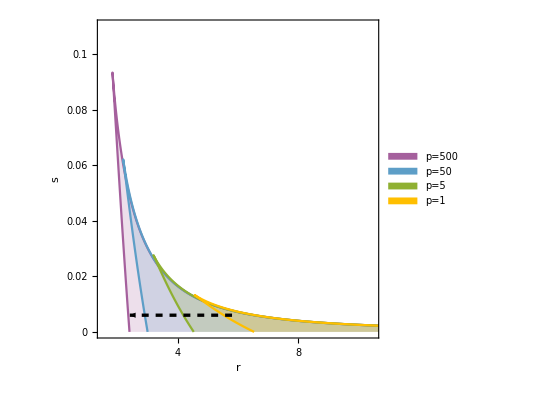

```mathematica
bistabilityp=ListLinePlot[{ddEspp500,ddEspp50,ddEspp5,ddEspp1},PlotStyle->{ColorData[97,9],ColorData[97,7],ColorData[97,3],ColorData[97,8]},PlotLegends->Placed[SwatchLegend[{"p=500","p=50","p=5","p=1"}],{Right,Top}],PlotRange->{{1.5,10.5},{0,0.11}},Filling->Bottom,Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["s",optsLabel2]},FrameTicks->{
{{{0,StyleForm["0",optsScale2],{0.03,0}},{0.02,StyleForm["0.02",optsScale2],{0.03,0}},{0.04,StyleForm["0.04",optsScale2],{0.03,0}},{0.06,StyleForm["0.06",optsScale2],{0.03,0}},{0.08,StyleForm["0.08",optsScale2],{0.03,0}},{0.1,StyleForm["0.1",optsScale2],{0.03,0}}},None},

{{{4,StyleForm["4",optsScale1],{0.03,0}},{6,StyleForm["6",optsScale1],{0.03,0}},{8,StyleForm["8",optsScale1],{0.03,0}},{10,StyleForm["10",optsScale1],{0.03,0}},{12,StyleForm["12",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}}},None}
},Epilog->{Dashed,Thickness[0.006],Arrow[{{5.8,0.006},{2.4,0.006}}]},AspectRatio->1]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

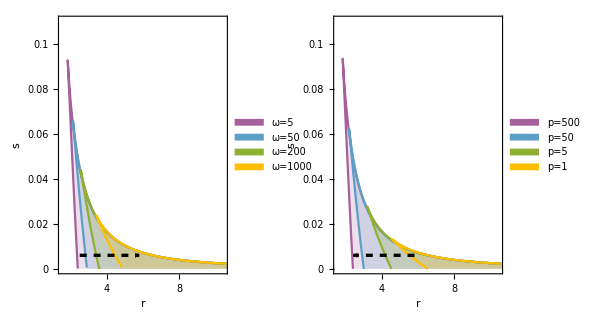

```mathematica
GraphicsArray[{bistabilityOmega,bistabilityp},ImageSize->600,Spacings->-55]
```